# One gluon radiation in onium-onium collision

Original code from Bin Wu
Created by Meijian Li on 2022.2.19
Last update on 2022.3.11

## Initialization

```mathematica
Clear["Global`*"]
```

### Global parameters

```mathematica
crntdir=NotebookDirectory[];
Nc=3;
ef=2/3;
eEM=Sqrt[4π 1/137];
Qc=2/3;
Qb=1/3;
```

### Style

```mathematica
font1="Times";
fontsizeXXL=22;
fontsizeXL=18;
fontsizeL=16;
fontsizeS=14;
fontsizeXS=12;
goldRatio=1-1/ⅇ;
```

```mathematica
color1=ColorData[71,1]
color2=ColorData[48,2]
color3=ColorData[24,5]
color4=ColorData[24,4]
color5=ColorData[34,3]
color6=ColorData[24,2]
color7=ColorData[24,3]
color8=ColorData[6,1]
color9=ColorData[112,4]
colorlist1={color1,color3,color6,color9,color8}
colorlist2={color1,color3,color8,color6}
```

Hue[0.94, 0.7, 0.9]

RGBColor[0.963806, 0.591257, 0.601724]

RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882]

RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843]

RGBColor[0.796078431372549, 0.803921568627451, 0.7725490196078432]

RGBColor[1., 0.7215686274509804, 0.2196078431372549]

RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883]

RGBColor[0.3411764705882353, 0.3411764705882353, 0.3411764705882353]

RGBColor[0., 0.596078, 0.109804]

{Hue[0.94, 0.7, 0.9],RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],RGBColor[1., 0.7215686274509804, 0.2196078431372549],RGBColor[0., 0.596078, 0.109804],RGBColor[0.3411764705882353, 0.3411764705882353, 0.3411764705882353]}

{Hue[0.94, 0.7, 0.9],RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],RGBColor[0.3411764705882353, 0.3411764705882353, 0.3411764705882353],RGBColor[1., 0.7215686274509804, 0.2196078431372549]}

## Hadron Light-front wavefunction (LFWF)

## Basis representation

References on convention
1. Phys.Rev.D 96 (2017) 1, 016022
2. W. Qian, S. Jia, Y. Li, and J. P. Vary, Phys. Rev. C 102, 055207 (2020)

### Basis function

#### Definition

Basis functions in the transverse and longitudinal spaces, respectively

```mathematica
(*Subscript[ϕ, mn](p^⊥)*)
bfphimm[n_,m_,k_,θ_,κ_]:=Piecewise[{{κ^-1 √((4π n!)/(n+Abs[m])! ) (k/κ )^Abs[m] Exp[-k^2/ (2 κ^2) ] LaguerreL[n,Abs[m],k^2/κ^2 ] Exp[ⅈ m θ],m!=0},{κ^-1 √(4π ) Exp[-k^2/ (2 κ^2) ] LaguerreL[n,0,k^2/κ^2 ] ,m==0}}];
(*Subscript[ϕ, mn](r^⊥)*)
bfphicor[n_,m_,r_,θ_,κ_]:=Piecewise[{{κ √(( n!)/(n+Abs[m])!π ) (r κ )^Abs[m] Exp[-κ^2 r^2/2 ] LaguerreL[n,Abs[m],r^2 κ^2 ] Exp[ⅈ m θ](-1)^n ⅈ^Abs[m],m!=0},{κ √(1/π ) Exp[-κ^2 r^2/2 ] LaguerreL[n,0,r^2 κ^2 ] (-1)^n ,m==0}}];

(*Subscript[χ, l](x)*)
bfchi[l_,x_,α_,β_]:=√((4 π (2 l+α+β+1) Gamma[l+1] Gamma[l+α+β+1])/(Gamma[l+α+1] Gamma[l+β+1])) x^(β/2) (1-x)^(α/2) JacobiP[l,α,β,2 x-1];
```

3D basis function in the momentum space, ψ_nml(k_⊥,x), and in the coordinate space (ψ̃)_nml(r_⊥,x)

```mathematica
(* Subscript[ψ, nml](k_⊥,x)
*)bfpsinmlmm[n_,m_,l_,k_,θ_,x_,κ_,mf_]:=bfphimm[n,m,k/Sqrt[x(1-x)],θ,κ]bfchi[l,x,(4 mf^2)/κ^2,(4 mf^2)/κ^2];
(* Subscript[ψ̃, nml](r_⊥,x)
*)bfpsinmlcor[n_,m_,l_,r_,θ_,x_,κ_,mf_]:=Sqrt[x(1-x)]bfphicor[n,m,r Sqrt[x(1-x)],θ,κ]bfchi[l,x,(4 mf^2)/κ^2,(4 mf^2)/κ^2];
```

LFWF with basis coefficients as a list of {n,m,l,s1,s2,...,coeffcient } with colnm the column number of the coefficient

```mathematica
Basis[{r_, x_},{n_,m_,l_},κ_:0.61,mf_:0.48,rUV_:∞]:=r Abs[bfpsinmlcor[n,m,l,r,0,x,κ,mf]]^2
```

```mathematica
Show[{Plot3D[Basis[{r, x},{0,0,0}],{r,0,25},{x,0,1},PlotRange->All],Graphics3D[{Thickness[0.01],Red,Line[{{3.5944311069321984,0.5,0},{3.5944311069321984,0.5,2.0}}] }]}]
```

-Graphics3D-

```mathematica
CheckNormal[{n_,m_,l_},κ_:0.61,mf_:0.48,rUV_:∞]:=NIntegrate[Basis[{r, x},{n,m,l},κ,mf,rUV],
{θ,0,2π},{r,0,rUV},{x,0,1}]
```

```mathematica
1/(4π)CheckNormal[{0,0,0}]
```

1.

So, the normalization is 4π!

```mathematica
rrms[{n_,m_,l_},κ_:0.61,mf_:0.48,rUV_:∞]:=Sqrt[NIntegrate[r^2 Basis[{r, x},{n,m,l},κ,mf,rUV],
{r,0,rUV},{x,0,1}]/NIntegrate[Basis[{r, x},{n,m,l},κ,mf,rUV],
{r,0,rUV},{x,0,1}]]
```

```mathematica
R000=rrms[{0,0,0}]
```

3.59443

```mathematica
lfwfmj[basiscoelist_,k_,θ_,x_,σ1_,σ2_,κ_,mf_,colnm_:1]:=Module[{s1,s2,n,m,l,w,sum=0,rnm},
rnm=Length[basiscoelist];
Do[s1=basiscoelist[[i,4]];
s2=basiscoelist[[i,5]];
If[s1==σ1&&s2==σ2,
n=basiscoelist[[i,1]];
m=basiscoelist[[i,2]];
l=basiscoelist[[i,3]];
w=basiscoelist[[i,5+colnm]];
sum=sum+w bfpsinmlmm[n,m,l,k,θ,x,κ,mf]],{i,1,rnm}];sum];
lfwfmjcor[basiscoelist_,r_,θ_,x_,σ1_,σ2_,κ_:1.34,mf_:1.27,colnm_:1]:=Module[{s1,s2,n,m,l,w,sum=0,rnm},
rnm=Length[basiscoelist];
Do[s1=basiscoelist[[i,4]];
s2=basiscoelist[[i,5]];
If[s1==σ1&&s2==σ2,
n=basiscoelist[[i,1]];
m=basiscoelist[[i,2]];
l=basiscoelist[[i,3]];
w=basiscoelist[[i,5+colnm]];
sum=sum+w bfpsinmlcor[n,m,l,r,θ,x,κ,mf]],{i,1,rnm}];sum];
lfwfListPUA[basiscoelist_,m_,s1_,s2_,colnm_:1]:=
Select[basiscoelist[[All,{1,2,3,4,5,5+colnm}]],#[[2]]==m&&#[[4]]==s1&&#[[5]]==s2&];
```

#### Plotting ϕ_nm(k_⊥)

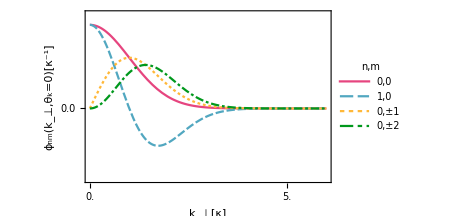

```mathematica
With[{κ=1.34,q2tck=.5,vtck=.4},
Plot[
{bfphimm[0,0,k,0,κ]κ,
bfphimm[1,0,k,0,κ]κ,
bfphimm[0,1,k,0,κ]κ,
bfphimm[0,2,k,0,κ]κ},{k,0,6κ},
PlotRange->{Full,{-3,4}},
PlotRangePadding->None,
ImageSize->350,
PlotTheme->"Monochrome",
PlotStyle->colorlist1,
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{Style["k_⊥[κ]",FontFamily->font1,fontsizeXL,Black],Style["ϕ_nm(k_⊥,θ_k=0)[κ^-1]",fontsizeXL,FontFamily->font1,Black]},
FrameTicks->{
{Table[If[Mod[i,5]==0,{vtck*i,NumberForm[vtck i,{3,1}],{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}],
Table[If[Mod[i,5]==0,{vtck*i,,{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}]},
{Table[If[Mod[i,2]==0,{κ q2tck i,NumberForm[q2tck i,3],{0,-0.025}},{κ q2tck i,,{0,-0.015}}],{i,0,40}],
Table[If[Mod[i,2]==0,{κ q2tck i,,{0,-0.025}},{κ q2tck i,,{0,-0.015}}],{i,0,40}]}},
PlotLegends->
Placed[
LineLegend[(Style[#,fontsizeS,FontFamily->font1]&)/@{"0,0","1,0","0,±1","0,±2"},LegendMarkerSize->fontsizeXXL,Spacings->0.5,
LegendFunction->(Framed[#1,FrameMargins->1,FrameStyle->LightGray,RoundingRadius->10]&),LegendLayout->{"Row",1},LegendLabel->Style["n,m",fontsizeL,FontFamily->font1]],{Right,Bottom}]
]
]
```

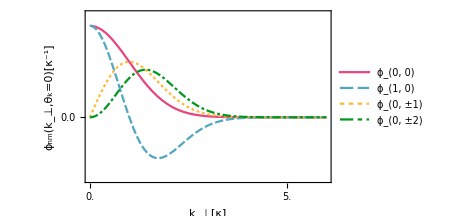

```mathematica
With[{κ=1.34,q2tck=.5,vtck=.4},
Plot[
{bfphimm[0,0,k,0,κ]κ,
bfphimm[1,0,k,0,κ]κ,
bfphimm[0,1,k,0,κ]κ,
bfphimm[0,2,k,0,κ]κ},{k,0,6κ},
PlotRange->{Full,{-2.4,4}},
PlotRangePadding->None,
ImageSize->350,
PlotTheme->"Monochrome",
PlotStyle->colorlist1,
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{Style["k_⊥[κ]",FontFamily->font1,fontsizeXL,Black],Style["ϕ_nm(k_⊥,θ_k=0)[κ^-1]",fontsizeXL,FontFamily->font1,Black]},
FrameTicks->{
{Table[If[Mod[i,5]==0,{vtck*i,NumberForm[vtck i,{3,1}],{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}],
Table[If[Mod[i,5]==0,{vtck*i,,{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}]},
{Table[If[Mod[i,2]==0,{κ q2tck i,NumberForm[q2tck i,3],{0,-0.025}},{κ q2tck i,,{0,-0.015}}],{i,0,40}],
Table[If[Mod[i,2]==0,{κ q2tck i,,{0,-0.025}},{κ q2tck i,,{0,-0.015}}],{i,0,40}]}},
PlotLegends->
Placed[
LineLegend[(Style[#,fontsizeS,FontFamily->font1]&)/@{"ϕ_(0, 0)","ϕ_(1, 0)","ϕ_(0, ±1)","ϕ_(0, ±2)"},LegendMarkerSize->fontsizeXXL,Spacings->0.5,
LegendFunction->(Framed[#1,FrameMargins->1,FrameStyle->LightGray,RoundingRadius->10]&),LegendLayout->{"Column",2}],{Right,Top}]
]
]
```

#### Plotting (ϕ̃)_nm(r_⊥)

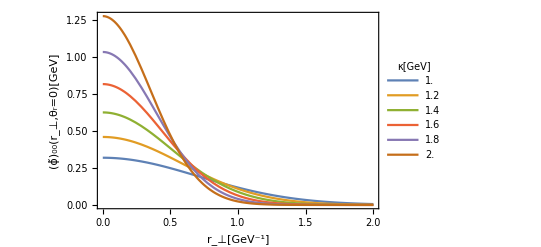

```mathematica
With[{q2tck=.5,vtck=.08},
Plot[Evaluate@Table[bfphicor[0,0,r,0,κ]bfphicor[0,0,r,0,κ],{κ,1,2,.2}],{r,0,2},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{Style["r_⊥[GeV^-1]",FontFamily->font1,fontsizeXL,Black],Style["(ϕ̃)_00(r_⊥,θ_r=0)[GeV]",fontsizeXL,FontFamily->font1,Black]},
PlotLegends->
Placed[
LineLegend[(Style[#,fontsizeS,FontFamily->font1]&)/@Table[κ,{κ,1,2,.2}],LegendMarkerSize->fontsizeXXL,Spacings->0.5,
LegendFunction->(Framed[#1,FrameMargins->1,FrameStyle->LightGray,RoundingRadius->10]&),LegendLayout->{"Row",3},LegendLabel->Style["κ[GeV]",fontsizeL,FontFamily->font1]],{Right,Top}]
]
]
```

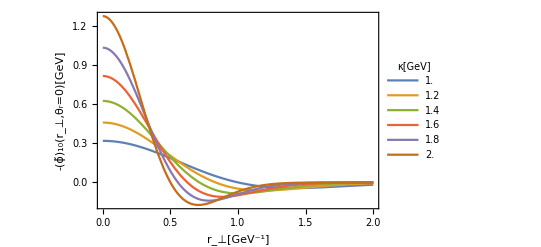

```mathematica
With[{q2tck=.5,vtck=.08},
Plot[Evaluate@Table[- bfphicor[1,0,r,0,κ]bfphicor[0,0,r,0,κ],{κ,1,2,.2}],{r,0,2},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{Style["r_⊥[GeV^-1]",FontFamily->font1,fontsizeXL,Black],Style["-(ϕ̃)_10(r_⊥,θ_r=0)[GeV]",fontsizeXL,FontFamily->font1,Black]},
PlotLegends->
Placed[
LineLegend[(Style[#,fontsizeS,FontFamily->font1]&)/@Table[κ,{κ,1,2,.2}],LegendMarkerSize->fontsizeXXL,Spacings->0.5,
LegendFunction->(Framed[#1,FrameMargins->1,FrameStyle->LightGray,RoundingRadius->10]&),LegendLayout->{"Row",3},LegendLabel->Style["κ[GeV]",fontsizeL,FontFamily->font1]],{Right,Top}]
]
]
```

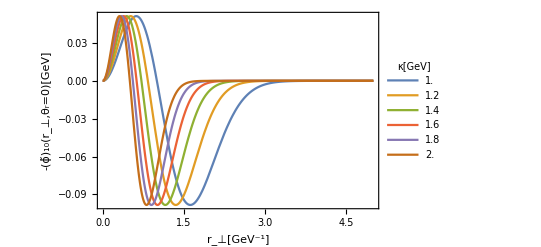

```mathematica
With[{q2tck=.5,vtck=.08},
Plot[Evaluate@Table[-r^2 bfphicor[1,0,r,0,κ]bfphicor[0,0,r,0,κ],{κ,1,2,.2}],{r,0,5},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{Style["r_⊥[GeV^-1]",FontFamily->font1,fontsizeXL,Black],Style["-r_⊥(ϕ̃)_10(r_⊥,θ_r=0)[GeV]",fontsizeXL,FontFamily->font1,Black]},
PlotLegends->
Placed[
LineLegend[(Style[#,fontsizeS,FontFamily->font1]&)/@Table[κ,{κ,1,2,.2}],LegendMarkerSize->fontsizeXXL,Spacings->0.5,
LegendFunction->(Framed[#1,FrameMargins->1,FrameStyle->LightGray,RoundingRadius->10]&),LegendLayout->{"Row",3},LegendLabel->Style["κ[GeV]",fontsizeL,FontFamily->font1]],{Right,Bottom}]
]
]
```

```mathematica
With[{q2tck=.5,vtck=.08},
Plot[Evaluate@Table[-r^2 bfphicor[1,0,r,0,κ]bfphicor[0,0,r,0,κ],{κ,1,2,.2}],{r,0,5},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{Style["r_⊥[GeV^-1]",FontFamily->font1,fontsizeXL,Black],Style["-(ϕ̃)_10(r_⊥,θ_r=0)[GeV]",fontsizeXL,FontFamily->font1,Black]},
PlotLegends->
Placed[
LineLegend[(Style[#,fontsizeS,FontFamily->font1]&)/@Table[κ,{κ,1,2,.2}],LegendMarkerSize->fontsizeXXL,Spacings->0.5,
LegendFunction->(Framed[#1,FrameMargins->1,FrameStyle->LightGray,RoundingRadius->10]&),LegendLayout->{"Row",3},LegendLabel->Style["κ[GeV]",fontsizeL,FontFamily->font1]],{Right,Bottom}]
]
]
```

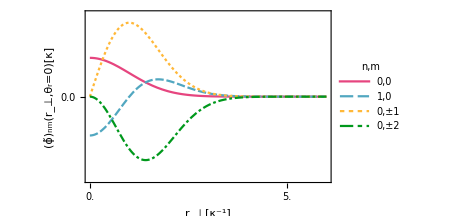

```mathematica
With[{κ=1.34,q2tck=.5,vtck=.08},
Plot[
{bfphicor[0,0,r,0,κ]/κ,
bfphicor[1,0,r,0,κ]/κ,
Im[bfphicor[0,1,r,0,κ]]/κ,
bfphicor[0,2,r,0,κ]/κ},{r,0,6/κ},
PlotRange->{Full,{-1.2,1.2}},
PlotRangePadding->None,
ImageSize->350,
PlotTheme->"Monochrome",
PlotStyle->colorlist1,
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{Style["r_⊥[κ^-1]",FontFamily->font1,fontsizeXL,Black],Style["(ϕ̃)_nm(r_⊥,θ_r=0)[κ]",fontsizeXL,FontFamily->font1,Black]},
FrameTicks->{
{Table[If[Mod[i,5]==0,{vtck*i,NumberForm[vtck i,{3,1}],{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}],
Table[If[Mod[i,5]==0,{vtck*i,,{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}]},
{Table[If[Mod[i,2]==0,{1/κ q2tck i,NumberForm[q2tck i,3],{0,-0.025}},{1/κ q2tck i,,{0,-0.015}}],{i,0,40}],
Table[If[Mod[i,2]==0,{1/κ q2tck i,,{0,-0.025}},{1/κ q2tck i,,{0,-0.015}}],{i,0,40}]}},
PlotLegends->
Placed[
LineLegend[(Style[#,fontsizeS,FontFamily->font1]&)/@{"0,0","1,0","0,±1","0,±2"},LegendMarkerSize->fontsizeXXL,Spacings->0.5,
LegendFunction->(Framed[#1,FrameMargins->1,FrameStyle->LightGray,RoundingRadius->10]&),LegendLayout->{"Row",1},LegendLabel->Style["n,m",fontsizeL,FontFamily->font1]],{Right,Bottom}]
]
]
```

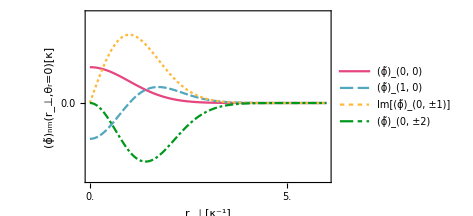

```mathematica
With[{κ=1.34,q2tck=.5,vtck=.1},
Plot[
{bfphicor[0,0,r,0,κ]/κ,
bfphicor[1,0,r,0,κ]/κ,
Im[bfphicor[0,1,r,0,κ]]/κ,
bfphicor[0,2,r,0,κ]/κ},{r,0,6/κ},
PlotRange->{Full,{-1.2,1.4}},
PlotRangePadding->None,
ImageSize->350,
PlotTheme->"Monochrome",
PlotStyle->colorlist1,
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{Style["r_⊥[κ^-1]",FontFamily->font1,fontsizeXL,Black],Style["(ϕ̃)_nm(r_⊥,θ_r=0)[κ]",fontsizeXL,FontFamily->font1,Black]},
FrameTicks->{
{Table[If[Mod[i,5]==0,{vtck*i,NumberForm[vtck i,{3,1}],{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}],
Table[If[Mod[i,5]==0,{vtck*i,,{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}]},
{Table[If[Mod[i,2]==0,{1/κ q2tck i,NumberForm[q2tck i,3],{0,-0.025}},{1/κ q2tck i,,{0,-0.015}}],{i,0,40}],
Table[If[Mod[i,2]==0,{1/κ q2tck i,,{0,-0.025}},{1/κ q2tck i,,{0,-0.015}}],{i,0,40}]}},
PlotLegends->
Placed[
LineLegend[(Style[#,fontsizeS,FontFamily->font1]&)/@{"(ϕ̃)_(0, 0)","(ϕ̃)_(1, 0)","Im[(ϕ̃)_(0, ±1)]","(ϕ̃)_(0, ±2)"},LegendMarkerSize->fontsizeXXL,Spacings->0.5,
LegendFunction->(Framed[#1,FrameMargins->1,FrameStyle->LightGray,RoundingRadius->10]&),LegendLayout->{"Column",2}],{Right,Top}]
]
]
```

#### Plotting χ_l(x)

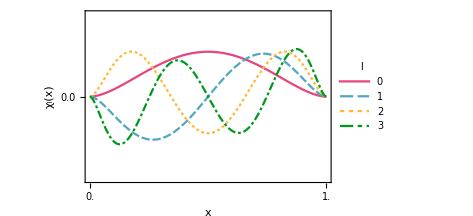

```mathematica
With[{κ=1.34,mf=1.27,q2tck=.1,vtck=.8},
α=4 mf^2/κ^2;
β=α;
Plot[
{bfchi[0,x,α,β],bfchi[1,x,α,β],bfchi[2,x,α,β],bfchi[3,x,α,β]},{x,0,1},
PlotRange->{Full,{-10,10}},
PlotRangePadding->None,
ImageSize->350,
PlotTheme->"Monochrome",
PlotStyle->colorlist1,
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{Style["x",FontFamily->font1,fontsizeXL,Black],Style["χ_l(x)",fontsizeXL,FontFamily->font1,Black]},
FrameTicks->{
{Table[If[Mod[i,5]==0,{vtck*i,NumberForm[vtck i,{3,1}],{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}],
Table[If[Mod[i,5]==0,{vtck*i,,{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}]},
{Table[If[Mod[i,2]==0,{ q2tck i,NumberForm[q2tck i,3],{0,-0.025}},{ q2tck i,,{0,-0.015}}],{i,0,40}],
Table[If[Mod[i,2]==0,{ q2tck i,,{0,-0.025}},{ q2tck i,,{0,-0.015}}],{i,0,40}]}},
PlotLegends->
Placed[
LineLegend[(Style[#,fontsizeS,FontFamily->font1]&)/@{0,1,2,3},LegendMarkerSize->fontsizeXXL,
Spacings->0.5,
LegendFunction->(Framed[#1,FrameMargins->1,FrameStyle->LightGray,RoundingRadius->10]&),LegendLayout->{"Row",1},LegendLabel->Style["l",fontsizeL,FontFamily->font1,Italic]],{Right,Bottom}
]
]
]
```

#### Plotting ψ_nml(k_⊥,x)

```mathematica
With[{mf=1.27,κ=1.34,q2tck=.5,vtck=1.6},
Plot3D[
{bfpsinmlmm[0,0,0,k,0,x,κ,mf],
bfpsinmlmm[1,0,0,k,0,x,κ,mf],
bfpsinmlmm[0,0,2,k,0,x,κ,mf],
(*bfpsinmlmm[0,1,1,k,0,x,κ,mf],*)
(*bfpsinmlmm[0,-1,1,k,0,x,κ,mf],*)
bfpsinmlmm[0,2,0,k,0,x,κ,mf](*,
bfpsinmlmm[0,-2,0,k,0,x,κ,mf]*)},{k,-3κ,3κ},{x,0,1},
PlotRange->All]
]
```

General::munfl: Exp[-62923.6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics3D-

```mathematica
"ψ_nml(k_⊥,θ_k=0,x=0.5) [κ^-1]"
```

```mathematica
With[{mf=1,κ=1,q2tck=.25,vtck=2,x=1/2},
Plot[
{bfpsinmlmm[0,0,0,k,0,x,κ,mf]κ,
bfpsinmlmm[1,0,0,k,0,x,κ,mf]κ,
bfpsinmlmm[0,0,2,k,0,x,κ,mf]κ,
(*bfpsinmlmm[0,1,1,k,0,x,κ,mf]κ,*)
(*bfpsinmlmm[0,-1,1,k,0,x,κ,mf]κ,*)
bfpsinmlmm[0,1,0,k,0,x,κ,mf]κ
(*,
bfpsinmlmm[0,-2,0,k,0,x,κ,mf]κ*)},{k,0,3κ},
PlotRange->{Full,{-18,24}},
PlotRangePadding->None,
ImageSize->400{1,goldRatio},
AspectRatio->1-1/ⅇ,
PlotTheme->"Monochrome",
PlotStyle->colorlist2,
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{Style["k_⊥[κ]",FontFamily->font1,fontsizeXL,Black],Style["ψ_nml((k⃗)_⊥,x) [κ^-1]",fontsizeXL,FontFamily->font1,Black]},
FrameTicks->{
{Table[If[Mod[i,5]==0,{vtck*i,NumberForm[vtck i,{3,1}],{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}],
Table[If[Mod[i,5]==0,{vtck*i,,{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}]},
{Table[If[Mod[i,2]==0,{κ q2tck i,NumberForm[q2tck i,3],{0,-0.025}},{κ q2tck i,,{0,-0.015}}],{i,0,40}],
Table[If[Mod[i,2]==0,{κ q2tck i,,{0,-0.025}},{κ q2tck i,,{0,-0.015}}],{i,0,40}]}},
PlotLegends->
Placed[
LineLegend[(Style[#,fontsizeS,FontFamily->font1]&)/@{"0,0,0","1,0,0","0,0,2",(*"0±11",*)"0,±1,0"},LegendMarkerSize->fontsizeXXL,Spacings->0.5,
LegendFunction->(Framed[#1,FrameMargins->1,FrameStyle->LightGray,RoundingRadius->10]&),LegendLayout->{"Column",2},LegendLabel->Style["n,m,l",fontsizeL,FontFamily->font1]],{Right,Top}](*,
Epilog->Inset[Style["θ_k=0, x=0.5",FontFamily->myfont,fontsizeL],Scaled[{.5,1.05}]],
PlotRangeClipping->False*)
]
]
```

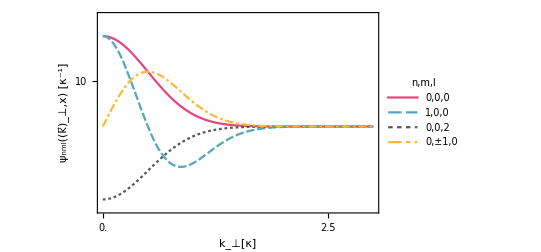
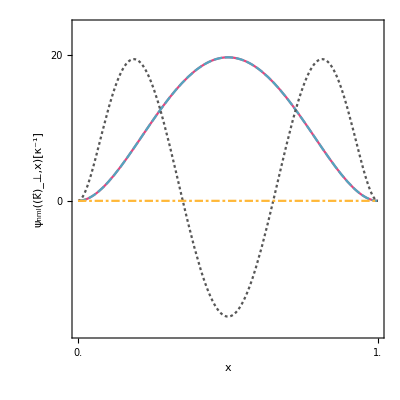

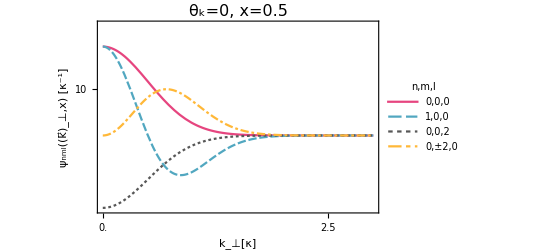
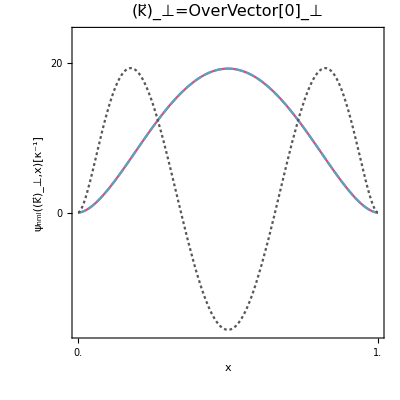

```mathematica
With[
{κ=1,mf=1,q2tck=.1,vtck=2,k=0},
α=4 mf^2/κ^2;
(*α//Print;*)
β=α;
Plot[
{bfpsinmlmm[0,0,0,k,0,x,κ,mf]κ,
bfpsinmlmm[1,0,0,k,0,x,κ,mf]κ,
bfpsinmlmm[0,0,2,k,0,x,κ,mf]κ,
bfpsinmlmm[0,1,0,k,0,x,κ,mf]κ
},{x,0,1},
PlotRange->{Full,{-18,24}},
PlotRangePadding->None,
ImageSize->goldRatio{400,400},
AspectRatio->1,
(*ImagePadding->{{80,20},{50,10}},*)
PlotTheme->"Monochrome",
PlotStyle->colorlist2,
(*PlotLabel->Style["k_⊥=0, θ_k=0","Title",FontFamily->myfont,fontsizeL],*)
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{
{Style["ψ_nml((k⃗)_⊥,x)[κ^-1]",fontsizeXL,FontFamily->font1,Black],None},
{Style["x",FontFamily->font1,fontsizeXL,Black],None}
},
FrameTicks->{
{Table[If[Mod[i,5]==0,{vtck*i,NumberForm[vtck i,{3,1}],{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}],
Table[If[Mod[i,5]==0,{vtck*i,,{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}]},
{Table[If[Mod[i,2]==0,{ q2tck i,NumberForm[q2tck i,3],{0,-0.025}},{ q2tck i,,{0,-0.015}}],{i,0,40}],
Table[If[Mod[i,2]==0,{ q2tck i,,{0,-0.025}},{ q2tck i,,{0,-0.015}}],{i,0,40}]}}(*,
Epilog->Inset[Style["(k⃗)_⊥=OverVector[0]_⊥",FontFamily->myfont,fontsizeL],Scaled[{.5,1.05}]],
PlotRangeClipping->False*)
]
]
```

-Graphics-

#### Plotting (ψ̃)_nml(r_⊥,x)

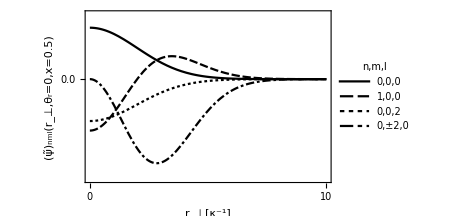

```mathematica
With[{mf=1.27,κ=1.34,q2tck=1,vtck=.4,x=1/2},
Plot[
{bfpsinmlcor[0,0,0,r,0,x,κ,mf],
bfpsinmlcor[1,0,0,r,0,x,κ,mf],
bfpsinmlcor[0,0,2,r,0,x,κ,mf],
bfpsinmlcor[0,2,0,r,0,x,κ,mf]},{r,0,10/κ},
PlotRange->{Full,{-4,2.6}},
PlotRangePadding->None,
ImageSize->350,
PlotTheme->"Monochrome",
(*PlotStyle->colorlist1,*)
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{Style["r_⊥[κ^-1]",FontFamily->font1,fontsizeXL,Black],Style["(ψ̃)_nml(r_⊥,θ_r=0,x=0.5)",fontsizeXL,FontFamily->font1,Black]},
FrameTicks->{
{Table[If[Mod[i,5]==0,{vtck*i,NumberForm[vtck i,{3,1}],{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}],
Table[If[Mod[i,5]==0,{vtck*i,,{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}]},
{Table[If[Mod[i,2]==0,{1/κ q2tck i,NumberForm[q2tck i,3],{0,-0.025}},{1/κ q2tck i,,{0,-0.015}}],{i,0,40}],
Table[If[Mod[i,2]==0,{1/κ q2tck i,,{0,-0.025}},{1/κ q2tck i,,{0,-0.015}}],{i,0,40}]}},
PlotLegends->
Placed[
LineLegend[(Style[#,fontsizeS,FontFamily->font1]&)/@{"0,0,0","1,0,0","0,0,2",(*"0±11",*)"0,±2,0"},LegendMarkerSize->fontsizeXXL,Spacings->0.5,
LegendFunction->(Framed[#1,FrameMargins->1,FrameStyle->LightGray,RoundingRadius->10]&),LegendLayout->{"Column",2},LegendLabel->Style["n,m,l",fontsizeL,FontFamily->font1]],{Right,Bottom}]
]
]
```

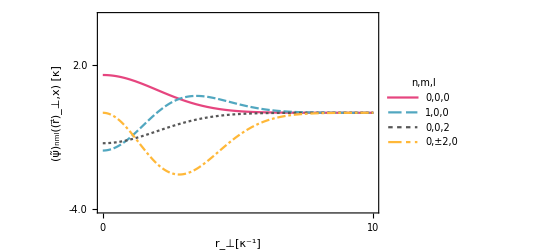

```mathematica
With[{mf=1,κ=1,q2tck=1,vtck=.4,x=1/2},
Plot[
{bfpsinmlcor[0,0,0,r,0,x,κ,mf]/κ,
bfpsinmlcor[1,0,0,r,0,x,κ,mf]/κ,
bfpsinmlcor[0,0,2,r,0,x,κ,mf]/κ,
bfpsinmlcor[0,-2,0,r,0,x,κ,mf]/κ},
{r,0,10/κ},
PlotRange->{Full,{-4,4}},
PlotRangePadding->None,
ImageSize->400{1,goldRatio},
AspectRatio->1-1/ⅇ,
PlotTheme->"Monochrome",
PlotStyle->colorlist2,
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{Style["r_⊥[κ^-1]",FontFamily->font1,fontsizeXL,Black],Style["(ψ̃)_nml((r⃗)_⊥,x) [κ]",fontsizeXL,FontFamily->font1,Black]},
FrameTicks->{
{Table[If[Mod[i,5]==0,{vtck*i,NumberForm[vtck i,{3,1}],{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}],
Table[If[Mod[i,5]==0,{vtck*i,,{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}]},
{Table[If[Mod[i,2]==0,{κ q2tck i,NumberForm[q2tck i,3],{0,-0.025}},{κ q2tck i,,{0,-0.015}}],{i,0,40}],
Table[If[Mod[i,2]==0,{κ q2tck i,,{0,-0.025}},{κ q2tck i,,{0,-0.015}}],{i,0,40}]}},
PlotLegends->
Placed[
LineLegend[(Style[#,fontsizeS,FontFamily->font1]&)/@{"0,0,0","1,0,0","0,0,2",(*"0±11",*)"0,±2,0"},LegendMarkerSize->fontsizeXXL,Spacings->0.5,
LegendFunction->(Framed[#1,FrameMargins->1,FrameStyle->LightGray,RoundingRadius->10]&),LegendLayout->{"Column",2},LegendLabel->Style["n,m,l",fontsizeL,FontFamily->font1]],{Right,Top}](*,
Epilog->Inset[Style["θ_k=0, x=0.5",FontFamily->myfont,fontsizeL],Scaled[{.5,1.05}]],
PlotRangeClipping->False*)
]
]
```

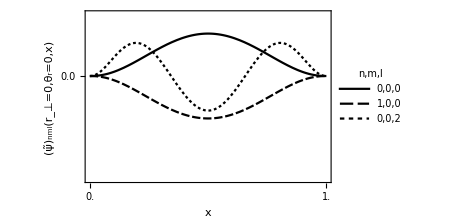

```mathematica
With[{mf=1.27,κ=1.34,q2tck=.1,vtck=.5,r=0},
Plot[
{
bfpsinmlcor[0,0,0,r,0,x,κ,mf],
bfpsinmlcor[1,0,0,r,0,x,κ,mf],
bfpsinmlcor[0,0,2,r,0,x,κ,mf]
},{x,0,1},
PlotRange->{Full,{-5,3}},
PlotRangePadding->None,
ImageSize->350,
PlotTheme->"Monochrome",
(*PlotStyle->colorlist1,*)
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{Style["x",FontFamily->font1,fontsizeXL,Black],Style["(ψ̃)_nml(r_⊥=0,θ_r=0,x)",fontsizeXL,FontFamily->font1,Black]},
FrameTicks->{
{Table[If[Mod[i,5]==0,{vtck*i,NumberForm[vtck i,{3,1}],{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}],
Table[If[Mod[i,5]==0,{vtck*i,,{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}]},
{Table[If[Mod[i,2]==0,{ q2tck i,NumberForm[q2tck i,3],{0,-0.025}},{ q2tck i,,{0,-0.015}}],{i,0,40}],
Table[If[Mod[i,2]==0,{ q2tck i,,{0,-0.025}},{ q2tck i,,{0,-0.015}}],{i,0,40}]}},
PlotLegends->
Placed[
LineLegend[(Style[#,fontsizeS,FontFamily->font1]&)/@{"0,0,0","1,0,0","0,0,2",(*"0±11",*)"0,±2,0"},LegendMarkerSize->fontsizeXXL,Spacings->0.5,
LegendFunction->(Framed[#1,FrameMargins->1,FrameStyle->LightGray,RoundingRadius->10]&),LegendLayout->{"Row",1},LegendLabel->Style["n,m,l",fontsizeL,FontFamily->font1]],{Right,Bottom}]
]
]
```

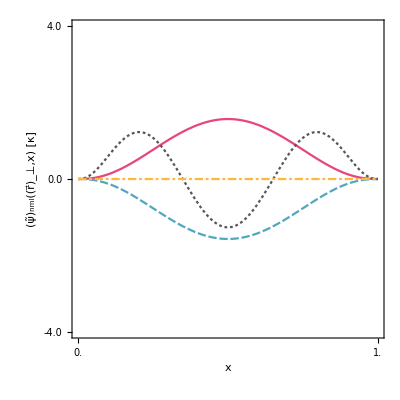

```mathematica
With[
{κ=1,mf=1,q2tck=.1,vtck=.4,r=0},
α=4 mf^2/κ^2;
(*α//Print;*)
β=α;
Plot[
{bfpsinmlcor[0,0,0,r,0,x,κ,mf]/κ,
bfpsinmlcor[1,0,0,r,0,x,κ,mf]/κ,
bfpsinmlcor[0,0,2,r,0,x,κ,mf]/κ,
bfpsinmlcor[0,-2,0,r,0,x,κ,mf]/κ
},{x,0,1},
PlotRange->{Full,{-4,4}},
PlotRangePadding->None,
ImageSize->goldRatio{400,400},
AspectRatio->1,
(*ImagePadding->{{80,20},{50,10}},*)
PlotTheme->"Monochrome",
PlotStyle->colorlist2,
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{
{Style["(ψ̃)_nml((r⃗)_⊥,x) [κ]",fontsizeXL,FontFamily->font1,Black],None},
{Style["x",FontFamily->font1,fontsizeXL,Black],None}
},
FrameTicks->{
{Table[If[Mod[i,5]==0,{vtck*i,NumberForm[vtck i,{3,1}],{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}],
Table[If[Mod[i,5]==0,{vtck*i,,{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}]},
{Table[If[Mod[i,2]==0,{ q2tck i,NumberForm[q2tck i,3],{0,-0.025}},{ q2tck i,,{0,-0.015}}],{i,0,40}],
Table[If[Mod[i,2]==0,{ q2tck i,,{0,-0.025}},{ q2tck i,,{0,-0.015}}],{i,0,40}]}}
]
]
```

### Model LFWF

Reference
1. e-Print: 2111.07087 [hep-ph]

To use the following LFWF as a function of (r, θ, x), call, e.g., 
lfwfmjcor[listWF1SVmj0,r,θ,x,1,-1,kappa,mf]

#### Basis states LF-W,0^(-+)

```mathematica
listWF1SPS={
{0,0,0,1,-1, Sqrt[1/2]},
{0,0,0,-1,1,-Sqrt[1/2]}};
listWF2SPS={
{1,0,0,1,-1, Sqrt[1/3]},
{1,0,0,-1,1,- Sqrt[1/3]},
{0,0,2,1,-1,- Sqrt[1/6]},
{0,0,2,-1,1, Sqrt[1/6]}};
listWF1PPS={
{0,-1,0,1,1,- Sqrt[1/2]},
{0,1,0,-1,-1,-Sqrt[1/2]}
};
```

#### Basis states LF-W,1^(--)

```mathematica
listWF1SVmj0={
{0,0,0,1,-1, Sqrt[1/2]},
{0,0,0,-1,1,Sqrt[1/2]}};
listWF1SVmj1={
{0,0,0,1,1,1}};
listWF1SVmjm1={
{0,0,0,-1,-1,1}};
```

```mathematica
listWF2SVmj0={
{1,0,0,1,-1, Sqrt[1/3]},
{1,0,0,-1,1, Sqrt[1/3]},
{0,0,2,1,-1,- Sqrt[1/6]},
{0,0,2,-1,1, -Sqrt[1/6]}};
listWF2SVmj1={
{1,0,0,1,1, Sqrt[2/3]},
{0,0,2,1,1,- Sqrt[1/3]}};
listWF2SVmjm1={
{1,0,0,-1,-1, Sqrt[2/3]},
{0,0,2,-1,-1,- Sqrt[1/3]}};
```

```mathematica
With[{d0=-Sqrt[2/5],d1=-Sqrt[3/5]},
listWF1DVmj0={
{0,-1,1,1,1,d1 Sqrt[1/2]},
{0,1,1,-1,-1,-d1 Sqrt[1/2]},
{0,0,2,1,-1,d0 Sqrt[1/3]},
{0,0,2,-1,1,d0 Sqrt[1/3]},
{1,0,0,1,-1,d0 Sqrt[1/6]},
{1,0,0,-1,1,d0 Sqrt[1/6]}
};
];
```

```mathematica
With[{a=Sqrt[3/5],b=-Sqrt[3/10],c=Sqrt[1/10]},
listWF1DVmj1={
{0,2,0,-1,-1,a},
{0,1,1,1,-1,-b Sqrt[1/2]},
{0,1,1,-1,1,-b Sqrt[1/2]},
{0,0,2,1,1,c Sqrt[2/3]},
{1,0,0,1,1,c Sqrt[1/3]}
};
listWF1DVmjm1={
{0,-2,0,1,1,a},
{0,-1,1,1,-1,b Sqrt[1/2]},
{0,-1,1,-1,1,b Sqrt[1/2]},
{0,0,2,-1,-1,c Sqrt[2/3]},
{1,0,0,-1,-1,c Sqrt[1/3]}
};
];
```

## The qq^-+qq^-→ qq^-+qq^-+g cross section

## Leading order calculation

```mathematica
anaLO[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}]:=1/4 Abs[Log[(((bx-x4+x1)^2+(by-y4+y1)^2)((bx-x3+x2)^2+(by-y3+y2)^2))/(((bx-x3+x1)^2+(by-y3+y1)^2)((bx-x4+x2)^2+(by-y4+y2)^2))]]^2
```

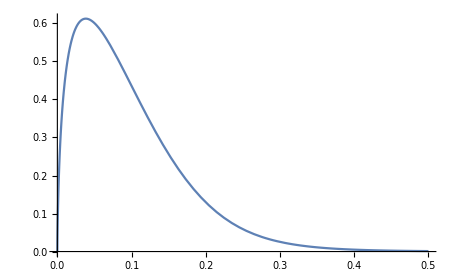

```mathematica
With[{by=0,rAx=0.4,rAy=0.4,rBx=0.4,rBy=0.4,xA=1/2,xB=1/2},
Module[{rA,θA,rB,θB,
x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y},
Plot[
x1x=bx+(1-xA)rAx ;
x1y=by+(1-xA)rAy ;
x2x=bx-xA rAx ;
x2y=by-xA rAy ;
x3x=(1-xB)rBx ;
x3y=(1-xB)rBy ;
x4x=-xB rBx ;
x4y=-xB rBy ;
(*{{bx,by},{x1x,x1y},{x2x,x2y},{x3x,x3y},{x4x,x4y}}//Print;*)
bx anaLO[{bx,by},{x1x,x1y},{x2x,x2y},{x3x,x3y},{x4x,x4y}],
{bx,0,.5},PlotRange->All]
]]
```

```mathematica
With[{rAx=0.4,rAy=0,rBx=0.4,rBy=0,xA=1/2,xB=1/2},
Module[{rA,θA,rB,θB,
x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y},
Plot3D[
x1x=bx+(1-xA)rAx ;
x1y=by+(1-xA)rAy ;
x2x=bx-xA rAx ;
x2y=by-xA rAy ;
x3x=(1-xB)rBx ;
x3y=(1-xB)rBy ;
x4x=-xB rBx ;
x4y=-xB rBy ;
(*{{bx,by},{x1x,x1y},{x2x,x2y},{x3x,x3y},{x4x,x4y}}//Print;*)
Sqrt[bx^2+by^2] anaLO[{bx,by},{x1x,x1y},{x2x,x2y},{x3x,x3y},{x4x,x4y}],
{bx,-0.5,.5},{by,-0.5,.5},PlotRange->All]
]]
```

-Graphics3D-

```mathematica
sigmatot[{nA_,mA_,lA_},{nB_,mB_,lB_},κ_:0.61,mf_:0.48,rUV_:∞]:=Module[{rA,xA,θA,rB,xB,θB,
rAx,rAy,rBx,rBy,
x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y},
(2π)/(4π)^2 NIntegrate[
rAx=rA Cos[θA];
rBx=rB Cos[θB];
rAy=rA Sin[θA];
rBy=rB Sin[θB];
x1x=b+(1-xA)rAx ;
x1y=(1-xA)rAy ;
x2x=b-xA rAx ;
x2y=-xA rAy ;
x3x=(1-xB)rBx ;
x3y=(1-xB)rBy ;
x4x=-xB rBx ;
x4y=-xB rBy ;
b rA rB anaLO[{b,0},{x1x,x1y},{x2x,x2y},{x3x,x3y},{x4x,x4y}]Abs[bfpsinmlcor[nA,mA,lA,rA,0,xA,κ,mf]]^2Abs[bfpsinmlcor[nB,mB,lB,rB,0,xB,κ,mf]]^2,
{θA,0,2π},{θB,0,2π},
{rA,0,rUV},{rB,0,rUV},
{xA,0,1},{xB,0,1},{b,0,rUV}]
]
(*Subscript[N, c]/(2 Subscript[α, s]^2 Subscript[C, F])dσ/(d^2 b)*)
FNsigmaLO[{bx_,by_},{nA_,mA_,lA_},{nB_,mB_,lB_},κ_:0.61,mf_:0.48,rUV_:∞]:=Module[{rA,xA,θA,rB,xB,θB,
rAx,rAy,rBx,rBy,
x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y},
1/(4π)^2 NIntegrate[
rAx=rA Cos[θA];
rBx=rB Cos[θB];
rAy=rA Sin[θA];
rBy=rB Sin[θB];
x1x=bx+(1-xA)rAx ;
x1y=by+(1-xA)rAy ;
x2x=bx-xA rAx ;
x2y=by-xA rAy ;
x3x=(1-xB)rBx ;
x3y=(1-xB)rBy ;
x4x=-xB rBx ;
x4y=-xB rBy ;
rA rB anaLO[{bx,by},{x1x,x1y},{x2x,x2y},{x3x,x3y},{x4x,x4y}]Abs[bfpsinmlcor[nA,mA,lA,rA,0,xA,κ,mf]]^2Abs[bfpsinmlcor[nB,mB,lB,rB,0,xB,κ,mf]]^2,
{θA,0,2π},{θB,0,2π},
{rA,0,rUV},{rB,0,rUV},
{xA,0,1},{xB,0,1}]
]
```

```mathematica
sigmatot[{0,0,0},{0,0,0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 345.848 and 80.0656 for the integral and error estimates.

13.7608

```mathematica
sigtot=13.760846990851322;
```

```mathematica
sigmaLOb=Table[{ibx,FNsigmaLO[{ibx,0},{0,0,0},{0,0,0}]},{ibx,0,20,.2}];
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 437.476 and 46.9469 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 379.555 and 29.7787 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 312.771 and 26.0599 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
sigmaLOb
```

{{0.,2.77035},{0.2,2.40356},{0.4,1.98065},{0.6,1.57588},{0.8,1.23025},{1.,0.957537},{1.2,0.737368},{1.4,0.568945},{1.6,0.435882},{1.8,0.337415},{2.,0.258969},{2.2,0.203193},{2.4,0.155563},{2.6,0.120565},{2.8,0.0949156},{3.,0.0745985},{3.2,0.0592125},{3.4,0.047006},{3.6,0.0378298},{3.8,0.0306853},{4.,0.0250935},{4.2,0.0205786},{4.4,0.0170037},{4.6,0.0140789},{4.8,0.0118089},{5.,0.00989116},{5.2,0.00842173},{5.4,0.00716864},{5.6,0.00615547},{5.8,0.0053062},{6.,0.00458985},{6.2,0.00399757},{6.4,0.00349259},{6.6,0.00305841},{6.8,0.00269614},{7.,0.00239129},{7.2,0.00211861},{7.4,0.00189529},{7.6,0.00169474},{7.8,0.00152184},{8.,0.00136855},{8.2,0.0012355},{8.4,0.00112026},{8.6,0.00101459},{8.8,0.000918255},{9.,0.00083735},{9.2,0.000766571},{9.4,0.000701511},{9.6,0.000643862},{9.8,0.000591731},{10.,0.000543189},{10.2,0.000501743},{10.4,0.000462401},{10.6,0.000427897},{10.8,0.000396353},{11.,0.000367744},{11.2,0.000341441},{11.4,0.000318849},{11.6,0.000297005},{11.8,0.000277048},{12.,0.000258705},{12.2,0.000241695},{12.4,0.000226361},{12.6,0.000212011},{12.8,0.000198966},{13.,0.000187248},{13.2,0.00017595},{13.4,0.000165549},{13.6,0.000155738},{13.8,0.000146748},{14.,0.000138413},{14.2,0.000130691},{14.4,0.000123475},{14.6,0.000116844},{14.8,0.000110524},{15.,0.000104723},{15.2,0.0000992469},{15.4,0.0000941519},{15.6,0.0000894608},{15.8,0.0000849852},{16.,0.0000808104},{16.2,0.0000768368},{16.4,0.0000731893},{16.6,0.0000697025},{16.8,0.000066456},{17.,0.0000633825},{17.2,0.0000604636},{17.4,0.0000576446},{17.6,0.0000550681},{17.8,0.0000526178},{18.,0.0000503079},{18.2,0.0000481202},{18.4,0.0000460455},{18.6,0.0000440845},{18.8,0.0000422355},{19.,0.0000404765},{19.2,0.000038806},{19.4,0.0000372326},{19.6,0.0000357245},{19.8,0.0000342897},{20.,0.0000329393}}

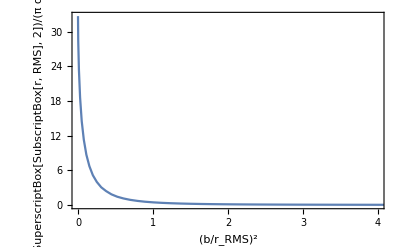

```mathematica
ListPlot[Transpose[{(sigmaLOb[[All,1]]/R000)^2,(4 π R000^2)/sigtot sigmaLOb[[All,2]]}],PlotRange->{{0,4},All},
Joined->True,
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{Style["(b/r_RMS)^2",FontFamily->font1,fontsizeXL,Black],Style["(4 SuperscriptBox[SubscriptBox[r, RMS], 2])/(π σ)dσ/db^2",fontsizeXL,FontFamily->font1,Black]}]
```

Check the black disk limit:

```mathematica
sigtot/(4 π R000^2)
```

0.0847569

Check normalization :

```mathematica
db=sigmaLOb[[2,1]]-sigmaLOb[[1,1]]
```

0.2

```mathematica
(2π)/sigtot( db*(Total[sigmaLOb[[2;;-2,1]]sigmaLOb[[2;;-2,2]]]+1/2(sigmaLOb[[1,1]]sigmaLOb[[1,2]]+sigmaLOb[[-1,1]]sigmaLOb[[-1,2]])))
```

0.989676

#### The Glauber model (taken from GlauberModel.nb)

```mathematica
dσd2bAA={{0.,0.},{0.018471766409471877,0.00443727304332474},{0.036943532818943754,0.00887454608664948},{0.055415299228415635,0.013311819129974221},{0.07388706563788751,0.01774909217329896},{0.09235883204735938,0.022186365216623698},{0.11083059845683127,0.026623638259948443},{0.12930236486630314,0.03106091130327318},{0.14777413127577502,0.03549818434659792},{0.1662458976852469,0.03993545738992266},{0.18471766409471876,0.044372730433247395},{0.20318943050419067,0.04881000347657215},{0.22166119691366254,0.053247276519896886},{0.2401329633231344,0.057684549563221624},{0.2586047297326063,0.06212182260654636},{0.27707649614207813,0.0665590956498711},{0.29554826255155003,0.07099636869319584},{0.31402002896102194,0.07543364173652058},{0.3324917953704938,0.07987091477984531},{0.3509635617799657,0.08430818782317005},{0.36943532818943753,0.08874546086649479},{0.38790709459890943,0.09318273390981953},{0.40637886100838133,0.0976200069531443},{0.42485062741785323,0.10205727999646903},{0.4433223938273251,0.10649455303979377},{0.4617941602367969,0.1109318260831185},{0.4802659266462688,0.11536909912644325},{0.49873769305574067,0.11980637216976799},{0.5172094594652126,0.12424364521309272},{0.5356812258746845,0.12868091825641748},{0.5541529922841563,0.1331181912997422},{0.5726247586936282,0.13755546434306695},{0.5910965251031001,0.14199273738639168},{0.609568291512572,0.14643001042971643},{0.6280400579220439,0.15086728347304115},{0.6465118243315157,0.1553045565163659},{0.6649835907409876,0.15974182955969063},{0.6834553571504595,0.16417910260301538},{0.7019271235599314,0.1686163756463401},{0.7203988899694033,0.17305364868966483},{0.7388706563788751,0.17749092173298958},{0.7573424227883471,0.18192819477631436},{0.7758141891978189,0.18636546781963906},{0.7942859556072907,0.19080274086296378},{0.8127577220167627,0.1952400139062886},{0.8312294884262345,0.19967728694961326},{0.8497012548357065,0.20411455999293807},{0.8681730212451783,0.2085518330362628},{0.8866447876546502,0.21298910607958754},{0.9051165540641221,0.21742637912291227},{0.9235883204735938,0.221863652166237},{0.9420600868830658,0.22630092520956174},{0.9605318532925377,0.2307381982528865},{0.9790036197020096,0.23517547129621125},{0.9974753861114813,0.23961274433953597},{1.0159471525209531,0.2440500173828607},{1.0344189189304251,0.24848729042618545},{1.052890685339897,0.25292456346951014},{1.071362451749369,0.25736183651283495},{1.0898342181588407,0.26179910955615965},{1.1083059845683125,0.2662363825994844},{1.1267777509777845,0.27067365564280915},{1.1452495173872563,0.2751109286861339},{1.1637212837967283,0.27954820172945866},{1.1821930502062001,0.28398547477278335},{1.200664816615672,0.2884227478161081},{1.219136583025144,0.29286002085943286},{1.2376083494346157,0.29729729390275755},{1.2560801158440877,0.3017345669460823},{1.2745518822535595,0.30617183998940706},{1.2930236486630313,0.3106091130327318},{1.3114954150725033,0.31504638607605656},{1.3299671814819751,0.31948365911938126},{1.3484389478914471,0.323920932162706},{1.366910714300919,0.32835820520603076},{1.3853824807103907,0.33279547824935546},{1.4038542471198627,0.3372327512926802},{1.4223260135293345,0.34167002433600496},{1.4407977799388065,0.34610729737932966},{1.4592695463482783,0.3505445704226545},{1.4777413127577501,0.35498184346597916},{1.496213079167222,0.35941911650930386},{1.5146848455766941,0.3638563895526287},{1.533156611986166,0.3682936625959535},{1.5516283783956377,0.3727309356392781},{1.5701001448051095,0.37716820868260287},{1.5885719112145813,0.38160548172592756},{1.6070436776240535,0.3860427547692524},{1.6255154440335253,0.3904800278125772},{1.6439872104429971,0.3949173008559019},{1.662458976852469,0.3993545738992265},{1.6809307432619407,0.4037918469425514},{1.699402509671413,0.40822911998587613},{1.7178742760808847,0.41266639302920083},{1.7363460424903565,0.4171036660725256},{1.7548178088998283,0.4215409391158502},{1.7732895753093003,0.4259782121591751},{1.791761341718772,0.43041548520249984},{1.8102331081282441,0.43485275824582453},{1.828704874537716,0.4392900312891492},{1.8471766409471877,0.443727304332474},{1.8656484073566597,0.4481645773757988},{1.8841201737661315,0.4526018504191235},{1.9025919401756035,0.45703912346244824},{1.9210637065850753,0.461476396505773},{1.939535472994547,0.4659136695490977},{1.958007239404019,0.4703509425924225},{1.976479005813491,0.4747882156357472},{1.9949507722229627,0.47922548867907194},{2.0134225386324345,0.48366276172239664},{2.0318943050419063,0.4881000347657214},{2.0503660714513785,0.49253730780904614},{2.0688378378608503,0.4969745808523709},{2.087309604270322,0.5014118538956956},{2.105781370679794,0.5058491269390203},{2.1242531370892657,0.510286399982345},{2.142724903498738,0.5147236730256699},{2.1611966699082097,0.5191609460689947},{2.1796684363176815,0.5235982191123193},{2.1981402027271533,0.528035492155644},{2.216611969136625,0.5324727651989688},{2.2350837355460973,0.5369100382422936},{2.253555501955569,0.5413473112856183},{2.272027268365041,0.5457845843289426},{2.2904990347745127,0.5502218573722514},{2.3089708011839845,0.5546591304153583},{2.3274425675934567,0.5590964034558356},{2.3459143340029285,0.5635336764664005},{2.3643861004124003,0.5679709491306736},{2.382857866821872,0.5724082180442689},{2.401329633231344,0.5768454455725815},{2.419801399640816,0.5812825246692104},{2.438273166050288,0.5857190353470327},{2.4567449324597597,0.5901523744752031},{2.4752166988692315,0.5945761552984428},{2.4936884652787032,0.5989705842599689},{2.5121602316881755,0.60330447929162},{2.5306319980976473,0.6074312887729146},{2.549103764507119,0.6112506079475988},{2.567575530916591,0.6145244376607928},{2.5860472973260626,0.6165943476628722},{2.604519063735535,0.6177123467622769},{2.6229908301450067,0.6150252631844842},{2.6414625965544785,0.6125605182030743},{2.6599343629639502,0.6041714595254272},{2.678406129373422,0.5929104730391398},{2.6968778957828943,0.5764783403809646},{2.715349662192366,0.5551685651445013},{2.733821428601838,0.5340567754764215},{2.7522931950113096,0.5020865631686888},{2.7707649614207814,0.4769080996860778},{2.7892367278302537,0.44192694632811175},{2.8077084942397255,0.4126226110525763},{2.8261802606491973,0.3793416789841733},{2.844652027058669,0.3394990755850958},{2.863123793468141,0.31322870483922766},{2.881595559877613,0.2823041727275673},{2.900067326287085,0.2494726162380707},{2.9185390926965566,0.22502626850377355},{2.9370108591060284,0.19905442739126625},{2.9554826255155002,0.17581154121668038},{2.9739543919249725,0.15794336371741163},{2.992426158334444,0.13526032417873043},{3.010897924743916,0.12065221637840472},{3.0293696911533883,0.10383953614720653},{3.0478414575628596,0.09199592827657642},{3.066313223972332,0.07754802535355824},{3.084784990381803,0.06882950233424767},{3.1032567567912754,0.059426487883666466},{3.1217285232007477,0.052308254850105956},{3.140200289610219,0.045471781004563436},{3.1586720560196913,0.03867609095272164},{3.1771438224291626,0.033144769838924455},{3.195615588838635,0.02815780467494951},{3.214087355248107,0.024544380695815434},{3.2325591216575784,0.021259304592091875},{3.2510308880670507,0.018170656630083964},{3.269502654476522,0.015425905121193715},{3.2879744208859942,0.013413410389607874},{3.3064461872954665,0.011443274260253213},{3.324917953704938,0.009754583810202893},{3.34338972011441,0.008566545581852414},{3.3618614865238814,0.0071331655109657995},{3.3803332529333536,0.006188036171699054},{3.398805019342826,0.005281165487698037},{3.417276785752297,0.0044946290209737175},{3.4357485521617694,0.0038610529901397113},{3.454220318571241,0.003340073477661633},{3.472692084980713,0.0028194475274266025},{3.4911638513901853,0.00245746189381842},{3.5096356177996566,0.0020721871081976102},{3.528107384209129,0.0017643840435773491},{3.5465791506186006,0.0014869028429888233},{3.5650509170280724,0.0012861570405104988},{3.583522683437544,0.00108947990974447},{3.601994449847016,0.0009362944791421393},{3.6204662162564882,0.0007857347468409895},{3.63893798266596,0.0006732982396732989},{3.657409749075432,0.0005714698474510706},{3.6758815154849036,0.0004867103758280573},{3.6943532818943754,0.0004117482768050282}};
```

```mathematica
dσd2b=Transpose[{sigmaLOb[[All,1]]/R000,(2 π R000)/sigtot sigmaLOb[[All,1]]sigmaLOb[[All,2]]}];
```

```mathematica
Needs["PlotLegends`"]
```

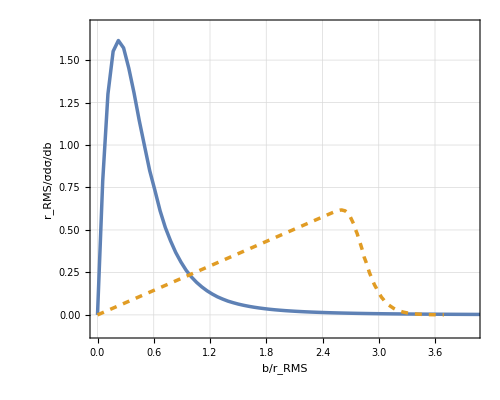

```mathematica
ListPlot[{dσd2b,dσd2bAA},PlotRange->{{0,4},{-0.1,1.7}},
(*PlotLegends->{"ππ","PbPb"},*)
AspectRatio->0.8,ImageSize->500,
Joined->True,
PlotStyle->{{Thickness[0.005]},{Thickness[0.005],Dashed}},
Frame->True,
GridLines->Automatic,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{Style["b/r_RMS",FontFamily->font1,fontsizeXL,Black],Style["r_RMS/σdσ/db",fontsizeXL,FontFamily->font1,Black]}]
```

check normalization :

```mathematica
Total[dσd2b[[All,2]]](dσd2b[[2,1]]-dσd2b[[1,1]])
Total[dσd2bAA[[All,2]]](dσd2bAA[[2,1]]-dσd2bAA[[1,1]])
```

0.989706

0.991482

#### Old result

```mathematica
sigmaLOb
```

{{0.,1827.05},{0.2,1340.57},{0.4,972.953},{0.6,695.29},{0.8,490.408},{1.,348.405},{1.2,256.468},{1.4,182.868},{1.6,132.572},{1.8,98.8208},{2.,73.09},{2.2,53.9946},{2.4,40.1087},{2.6,31.1969},{2.8,23.9649},{3.,18.4278},{3.2,14.4537},{3.4,11.401},{3.6,9.07126},{3.8,7.40173},{4.,5.97249},{4.2,4.91327},{4.4,4.04933},{4.6,3.35529},{4.8,2.81748},{5.,2.36814},{5.2,2.00721},{5.4,1.70442},{5.6,1.46673},{5.8,1.27129},{6.,1.10159},{6.2,0.958229},{6.4,0.837259},{6.6,0.751842},{6.8,0.647885},{7.,0.572113},{7.2,0.506918},{7.4,0.454836},{7.6,0.405614},{7.8,0.363549},{8.,0.325875},{8.2,0.294819},{8.4,0.267069},{8.6,0.241935},{8.8,0.219899},{9.,0.200679},{9.2,0.182997},{9.4,0.167343},{9.6,0.153466},{9.8,0.140901},{10.,0.129904},{10.2,0.119789},{10.4,0.110783},{10.6,0.102423},{10.8,0.094851},{11.,0.0880462},{11.2,0.0817664},{11.4,0.0760779},{11.6,0.0707358},{11.8,0.0661432},{12.,0.061786},{12.2,0.0576153},{12.4,0.0540063},{12.6,0.0506109},{12.8,0.0474666},{13.,0.0445592},{13.2,0.041853},{13.4,0.0393733},{13.6,0.037107},{13.8,0.0349648},{14.,0.0329907},{14.2,0.0311282},{14.4,0.0294135},{14.6,0.0278247},{14.8,0.0263308},{15.,0.0249129},{15.2,0.0236119},{15.4,0.0223926},{15.6,0.0212603},{15.8,0.0201914},{16.,0.0191864},{16.2,0.0182553},{16.4,0.0173653},{16.6,0.0165378},{16.8,0.0157769},{17.,0.0150413},{17.2,0.0143432},{17.4,0.013684},{17.6,0.0130715},{17.8,0.0124894},{18.,0.0119325},{18.2,0.0114184},{18.4,0.0109305},{18.6,0.010462},{18.8,0.0100206},{19.,0.00960802},{19.2,0.00921151},{19.4,0.00882572},{19.6,0.00847352},{19.8,0.00813418},{20.,0.00781175}}

{{0.,1827.05},{0.2,1340.57},{0.4,972.953},{0.6,695.29},{0.8,490.408},{1.,348.405},{1.2,256.468},{1.4,182.868},{1.6,132.572},{1.8,98.8208},{2.,73.09},{2.2,53.9946},{2.4,40.1087},{2.6,31.1969},{2.8,23.9649},{3.,18.4278},{3.2,14.4537},{3.4,11.401},{3.6,9.07126},{3.8,7.40173},{4.,5.97249},{4.2,4.91327},{4.4,4.04933},{4.6,3.35529},{4.8,2.81748},{5.,2.36814},{5.2,2.00721},{5.4,1.70442},{5.6,1.46673},{5.8,1.27129},{6.,1.10159},{6.2,0.958229},{6.4,0.837259},{6.6,0.751842},{6.8,0.647885},{7.,0.572113},{7.2,0.506918},{7.4,0.454836},{7.6,0.405614},{7.8,0.363549},{8.,0.325875},{8.2,0.294819},{8.4,0.267069},{8.6,0.241935},{8.8,0.219899},{9.,0.200679},{9.2,0.182997},{9.4,0.167343},{9.6,0.153466},{9.8,0.140901},{10.,0.129904},{10.2,0.119789},{10.4,0.110783},{10.6,0.102423},{10.8,0.094851},{11.,0.0880462},{11.2,0.0817664},{11.4,0.0760779},{11.6,0.0707358},{11.8,0.0661432},{12.,0.061786},{12.2,0.0576153},{12.4,0.0540063},{12.6,0.0506109},{12.8,0.0474666},{13.,0.0445592},{13.2,0.041853},{13.4,0.0393733},{13.6,0.037107},{13.8,0.0349648},{14.,0.0329907},{14.2,0.0311282},{14.4,0.0294135},{14.6,0.0278247},{14.8,0.0263308},{15.,0.0249129},{15.2,0.0236119},{15.4,0.0223926},{15.6,0.0212603},{15.8,0.0201914},{16.,0.0191864},{16.2,0.0182553},{16.4,0.0173653},{16.6,0.0165378},{16.8,0.0157769},{17.,0.0150413},{17.2,0.0143432},{17.4,0.013684},{17.6,0.0130715},{17.8,0.0124894},{18.,0.0119325},{18.2,0.0114184},{18.4,0.0109305},{18.6,0.010462},{18.8,0.0100206},{19.,0.00960802},{19.2,0.00921151},{19.4,0.00882572},{19.6,0.00847352},{19.8,0.00813418},{20.,0.00781175}}

```mathematica
sigmaLOb
```

```mathematica
sigmaLObML:={{0.,1827.0454777245034},{0.2,1340.5734114084855},{0.4,972.9533653821983},{0.6000000000000001,695.290311684396},{0.8,490.4078170835704},{1.,348.4054012412417},{1.2000000000000002,256.46815301191873},{1.4000000000000001,182.86819417664674},{1.6,132.57218090011088},{1.8,98.82075762160596},{2.,73.09000914167947},{2.2,53.99462438503211},{2.4000000000000004,40.10871700470757},{2.6,31.19689668924144},{2.8000000000000003,23.964946585750933},{3.,18.427831874649513},{3.2,14.453663086594446},{3.4000000000000004,11.401013883245716},{3.6,9.071258070734448},{3.8000000000000003,7.40173109094743},{4.,5.972492453980269},{4.2,4.913267854290068},{4.4,4.049325249765297},{4.6000000000000005,3.355285748096215},{4.800000000000001,2.8174764322557992},{5.,2.3681361440450215},{5.2,2.0072095261873635},{5.4,1.7044173453977403},{5.6000000000000005,1.4667306202115857},{5.800000000000001,1.271290754636483},{6.,1.101594267299241},{6.2,0.9582294676810532},{6.4,0.8372585668491614},{6.6000000000000005,0.7518423220324664},{6.800000000000001,0.6478850935776344},{7.,0.5721127477799315},{7.2,0.5069179828249647},{7.4,0.4548360729728848},{7.6000000000000005,0.40561359135372366},{7.800000000000001,0.3635490851092245},{8.,0.32587512777386013},{8.200000000000001,0.29481851553555083},{8.4,0.26706943943520617},{8.6,0.24193491104588635},{8.8,0.21989884025466971},{9.,0.20067881643795765},{9.200000000000001,0.18299726703242997},{9.4,0.16734295886564735},{9.600000000000001,0.15346631750346418},{9.8,0.14090082974849066},{10.,0.12990404507712913},{10.200000000000001,0.11978860965380417},{10.4,0.11078279873118452},{10.600000000000001,0.10242324271604526},{10.8,0.09485097775811696},{11.,0.08804618669957125},{11.200000000000001,0.08176641804105973},{11.4,0.07607787715139155},{11.600000000000001,0.0707357598803036},{11.8,0.06614320398272958},{12.,0.06178600806526301},{12.200000000000001,0.05761534140711161},{12.4,0.05400630522401898},{12.600000000000001,0.05061087327516826},{12.8,0.04746663816915197},{13.,0.04455916124696806},{13.200000000000001,0.04185299796978808},{13.4,0.039373256842332754},{13.600000000000001,0.03710704886817407},{13.8,0.034964829794445804},{14.,0.03299073956874003},{14.200000000000001,0.03112824807621877},{14.4,0.029413530516963982},{14.600000000000001,0.027824680008101167},{14.8,0.026330843799110718},{15.,0.024912886733689937},{15.200000000000001,0.02361186354013613},{15.4,0.022392631532283536},{15.600000000000001,0.021260336731514944},{15.8,0.020191394501594524},{16.,0.019186410350719288},{16.2,0.018255286691755704},{16.400000000000002,0.017365325689863993},{16.6,0.01653780884455721},{16.8,0.015776892806862442},{17.,0.015041293542169949},{17.2,0.014343219711342574},{17.400000000000002,0.013684027481704535},{17.6,0.013071543885977213},{17.8,0.012489408348070686},{18.,0.011932460931546728},{18.2,0.011418437874095064},{18.400000000000002,0.010930543616357384},{18.6,0.010462018154981656},{18.8,0.010020608802165303},{19.,0.00960801926253446},{19.200000000000003,0.009211507436742625},{19.400000000000002,0.008825719855735274},{19.6,0.008473516368042638},{19.8,0.008134182996595829},{20.,0.007811753164455577}}
```

```mathematica
sigmaLObML[[1,2]]/sigmaLOb[[1,2]]
```

20.383

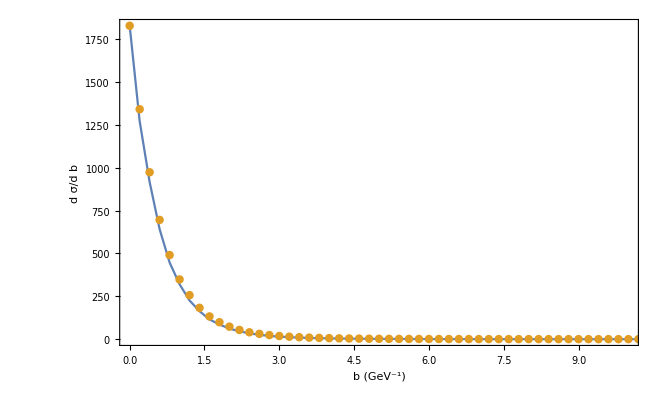

```mathematica
ListPlot[{Transpose[{sigmaLOb[[All,1]],sigmaLObML[[1,2]]/sigmaLOb[[1,2]] sigmaLOb[[All,2]]}],sigmaLObML},PlotRange->{{0,10},All},
Joined->{True,False},
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{Style["b (GeV^-1)",FontFamily->font1,fontsizeXL,Black],Style["d σ/d b",fontsizeXL,FontFamily->font1,Black]}]
```

## Full calculation

### Calculation of the integral

```mathematica
FourierTransform[1/(kx^2+ky^2),{kx,ky},{rx,ry}]
```

1/2 (-HeavisideTheta[-rx] (2 Log[-rx]+Log[1+ry^2/rx^2])-HeavisideTheta[rx] (2 Log[rx]+Log[1+ry^2/rx^2]))

```mathematica
FourierTransform[1/(kx^2+ky^2),kx,x]
```

1/(2 ky)ⅇ^(-ky x) √(π/2) ((-1+ⅇ^(2 ky x)) Sign[x] (-1+Sign[Abs[Re[ky]]])+2 (ⅇ^(2 ky x) HeavisideTheta[-x Sign[Re[ky]]]+HeavisideTheta[x Sign[Re[ky]]]) Sign[Re[ky]])

```mathematica
FourierTransform[1/(2 ky)ⅇ^(-ky x) √(π/2) ((-1+ⅇ^(2 ky x)) Sign[x] (-1+Sign[Abs[Re[ky]]])+2 (ⅇ^(2 ky x) HeavisideTheta[-x Sign[Re[ky]]]+HeavisideTheta[x Sign[Re[ky]]]) Sign[Re[ky]]),ky,y]
```

1/2 (-HeavisideTheta[-x] (2 Log[-x]+Log[1+y^2/x^2])-HeavisideTheta[x] (2 Log[x]+Log[1+y^2/x^2]))

```mathematica
FullSimplify[1/2 (-HeavisideTheta[-x] (2 Log[-x]+Log[1+y^2/x^2])-HeavisideTheta[x] (2 Log[x]+Log[1+y^2/x^2]))]
```

-HeavisideTheta[-x] Log[-x]-HeavisideTheta[x] Log[x]-1/2 (HeavisideTheta[-x]+HeavisideTheta[x]) Log[1+y^2/x^2]

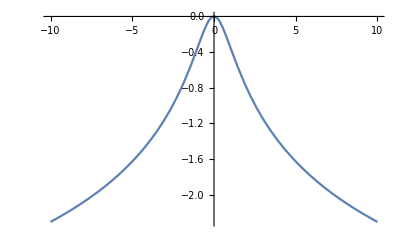

```mathematica
With[{y=1},Plot[-HeavisideTheta[-x] Log[-x]-HeavisideTheta[x] Log[x]-1/2 (HeavisideTheta[-x]+HeavisideTheta[x]) Log[1+y^2/x^2],{x,-10,10}]]
```

```mathematica
testf[a_:1,b_:1]:=a+b
```

```mathematica
testf[1,2]
```

3

```mathematica
Drop[.001]
```

0.001

```mathematica
ft01=-EulerGamma-Log[r]
```

-EulerGamma-Log[r]

We would like to evaluate the Fourier Transform of

```mathematica
itg:=1/(kx^2+ky^2)1/((kx-lx)^2+(ky-ly)^2)
```

```mathematica
FourierTransform[1/(kx^2+ky^2)1/((kx-lx)^2+(ky-ly)^2),{kx,ky},{x,y}]
```

$Aborted

Since it is scalar, we put set {x,y}/r as the y axis with r the modulus of {x,y}. Then it is trivial to integrate out kx firxt.

It is trivial to integrate out, say, kx :

```mathematica
intkxana[ky_,{lx_,ly_}]=FullSimplify[I HeavisideTheta[ky]Residue[itg,{kx,I ky}]]+FullSimplify[I HeavisideTheta[-ky]Residue[itg,{kx,-I ky}]]+FullSimplify[I HeavisideTheta[ky-ly]Residue[itg,{kx,lx+I (ky-ly)}]]+FullSimplify[I HeavisideTheta[-ky+ly]Residue[itg,{kx,lx-I (ky-ly)}]]
```

0

```mathematica
ftkx:=(ⅈ HeavisideTheta[-ky])/(2 ky (2 ky-ⅈ lx-ly) (lx+ⅈ ly))+(ⅈ HeavisideTheta[ky])/(2 ky (2 ky+ⅈ lx-ly) (lx-ⅈ ly))+HeavisideTheta[ky-ly]/(2 (ky-ly) (2 ky-ⅈ lx-ly) (ⅈ lx+ly))-HeavisideTheta[-ky+ly]/(2 (ky-ly) (lx+ⅈ ly) (-2 ⅈ ky+lx+ⅈ ly))
```

```mathematica
intkx[ky_,{lx_,ly_}]:=1/(2π)NIntegrate[1/(kx^2+ky^2)1/((kx-lx)^2+(ky-ly)^2),{kx,-Infinity,Infinity}]
```

```mathematica
cond:=r>0&&x∈Reals&&y∈Reals&&2 π>ϕ>0 &&ky∈Reals&&lx∈Reals&&ly∈Reals
```

the first term

#### Term 1

```mathematica
ftkx[[1]]
```

(ⅈ HeavisideTheta[-ky])/(2 ky (2 ky-ⅈ lx-ly) (lx+ⅈ ly))

```mathematica
dem:=2 ky (2 ky-ⅈ lx-ly) (lx+ⅈ ly)
```

```mathematica
apky= Apart[((lx-ⅈ ly) (lx+ⅈ ly))/dem,ky]
```

ⅈ/(2 ky)-ⅈ/(2 ky-ⅈ lx-ly)

```mathematica
term11=Assuming[cond,1/l^2 FourierTransform[ftkx[[1]] dem apky[[1]],ky,r]//FullSimplify]
```

-(EulerGamma+(ⅈ π)/2+Log[r])/(2 l^2 √(2 π))

```mathematica
ftkx[[1]] dem apky[[2]]
```

HeavisideTheta[-ky]/(2 ky-ⅈ lx-ly)

```mathematica
Numerator[ftkx[[1]] dem apky[[2]]]
```

HeavisideTheta[-ky]

```mathematica
FullSimplify[Expand[√(2 π)FourierTransform[HeavisideTheta[-ky],ky,y]]]
Assuming[cond,FullSimplify[Expand[√(2 π)FourierTransform[1/(2 ky-ⅈ lx-ly),ky,y]]]]
```

-ⅈ/y+π DiracDelta[y]

ⅈ ⅇ^(-1/2 (lx-ⅈ ly) y) π HeavisideTheta[y Sign[Im[ly]+Re[lx]]] Sign[Im[ly]+Re[lx]]

```mathematica
Integrate[ⅈ ⅇ^(-1/2 (lx-ⅈ ly) y) π HeavisideTheta[y ](-ⅈ/(r-y)+π DiracDelta[r-y]) ,{y,-Infinity,Infinity}]
Integrate[-ⅈ ⅇ^(-1/2 (lx-ⅈ ly) y) π HeavisideTheta[-y ](-ⅈ/(r-y)+π DiracDelta[r-y]) ,{y,-Infinity,Infinity}]
```

ConditionalExpression[-ⅇ^(-1/2 (lx-ⅈ ly) r) π Gamma[0,-1/2 (lx-ⅈ ly) r], Re[r]<0&&Im[r]==0&&Im[ly]+Re[lx]>0]

ConditionalExpression[-ⅇ^(-1/2 (lx-ⅈ ly) r) π Gamma[0,-1/2 (lx-ⅈ ly) r], Im[ly]+Re[lx]<0&&Re[r]>0&&Im[r]==0]

```mathematica
t12:=-1/(2 π Sqrt[2π] l^2)ⅇ^(-1/2 (lx-ⅈ ly) r) π Gamma[0,-1/2 (lx-ⅈ ly) r]
```

```mathematica
term1=term11+t12
```

-(ⅇ^(-1/2 (lx-ⅈ ly) r) Gamma[0,-1/2 (lx-ⅈ ly) r])/(2 l^2 √(2 π))-(EulerGamma+(ⅈ π)/2+Log[r])/(2 l^2 √(2 π))

#### Term 2

```mathematica
ftkx
```

(ⅈ HeavisideTheta[-ky])/(2 ky (2 ky-ⅈ lx-ly) (lx+ⅈ ly))+(ⅈ HeavisideTheta[ky])/(2 ky (2 ky+ⅈ lx-ly) (lx-ⅈ ly))+HeavisideTheta[ky-ly]/(2 (ky-ly) (2 ky-ⅈ lx-ly) (ⅈ lx+ly))-HeavisideTheta[-ky+ly]/(2 (ky-ly) (lx+ⅈ ly) (-2 ⅈ ky+lx+ⅈ ly))

```mathematica
ftkx[[2]]
```

(ⅈ HeavisideTheta[ky])/(2 ky (2 ky+ⅈ lx-ly) (lx-ⅈ ly))

```mathematica
Denominator[ftkx[[2]]]
```

2 ky (2 ky+ⅈ lx-ly) (lx-ⅈ ly)

```mathematica
apky= Apart[((lx-ⅈ ly) (lx+ⅈ ly))/Denominator[ftkx[[2]]],ky]
```

-ⅈ/(2 ky)+ⅈ/(2 ky+ⅈ lx-ly)

```mathematica
Numerator[ftkx[[2]]] apky[[1]]
```

HeavisideTheta[ky]/(2 ky)

```mathematica
term21=Assuming[cond,1/l^2 FourierTransform[Numerator[ftkx[[2]]] apky[[1]],ky,r]//FullSimplify]
```

(ⅈ (2 ⅈ EulerGamma+π+2 ⅈ Log[r]))/(4 l^2 √(2 π))

```mathematica
term22=Assuming[cond,1/(lx^2+ly^2)FourierTransform[Numerator[ftkx[[2]]]apky[[2]],ky,r]//FullSimplify]
```

(ⅇ^(1/2 (lx+ⅈ ly) r) (-ⅈ π+2 CosIntegral[1/2 ⅈ (lx+ⅈ ly) r]-2 SinhIntegral[1/2 (lx+ⅈ ly) r]))/(4 (lx^2+ly^2) √(2 π))

```mathematica
FullSimplify[Expand[√(2 π)FourierTransform[Numerator[ftkx[[2]]] ,ky,y]]]
Assuming[cond,FullSimplify[Expand[√(2 π)FourierTransform[apky[[2]],ky,y]]]]
```

-1/y+ⅈ π DiracDelta[y]

ⅇ^(1/2 (lx+ⅈ ly) y) π HeavisideTheta[-y Sign[lx]] Sign[lx]

```mathematica
Integrate[ⅇ^(1/2 (lx+ⅈ ly) y) π HeavisideTheta[-y ] (-1/(r-y)+ⅈ π DiracDelta[r-y]) ,{y,-Infinity,Infinity}]
Integrate[-ⅇ^(1/2 (lx+ⅈ ly) y) π HeavisideTheta[y](-1/(r-y)+ⅈ π DiracDelta[r-y]) ,{y,-Infinity,Infinity}]
```

ConditionalExpression[-ⅇ^(1/2 (lx+ⅈ ly) r) π Gamma[0,1/2 (lx+ⅈ ly) r], Re[lx]>Im[ly]&&Re[r]>0&&Im[r]==0]

ConditionalExpression[-ⅇ^(1/2 (lx+ⅈ ly) r) π Gamma[0,1/2 (lx+ⅈ ly) r], Re[r]<0&&Im[r]==0&&Re[lx]<Im[ly]]

```mathematica
t22:=1/(2 π Sqrt[2π] l^2)(-ⅇ^(1/2 (lx+ⅈ ly) r) π Gamma[0,1/2 (lx+ⅈ ly) r])
```

```mathematica
term22/.{lx->3,ly->0.3,r->1.0}
t22/.{lx->3,ly->0.3,r->1.0}
```

-0.00978113+0.000714427 ⅈ

-(0.0889105-0.00649414 ⅈ)/l^2

```mathematica
term2=term21+t22
```

-(ⅇ^(1/2 (lx+ⅈ ly) r) Gamma[0,1/2 (lx+ⅈ ly) r])/(2 l^2 √(2 π))+(ⅈ (2 ⅈ EulerGamma+π+2 ⅈ Log[r]))/(4 l^2 √(2 π))

```mathematica
ftkx[[1;;2]]
```

(ⅈ HeavisideTheta[-ky])/(2 ky (2 ky-ⅈ lx-ly) (lx+ⅈ ly))+(ⅈ HeavisideTheta[ky])/(2 ky (2 ky+ⅈ lx-ly) (lx-ⅈ ly))

From this, we can see how the two related to each other :

```mathematica
(Assuming[cond,Conjugate[ftkx[[1]]]//FullSimplify]/.Conjugate[x_]->x/.{ky->-ky}//FullSimplify)/.{lx->-lx,ly->-ly}//FullSimplify
```

(ⅈ HeavisideTheta[ky])/(2 ky (2 ky+ⅈ lx-ly) (lx-ⅈ ly))

```mathematica
(ⅈ HeavisideTheta[ky])/(2 ky (2 ky+ⅈ lx-ly) (lx-ⅈ ly))-ftkx[[2]]
```

0

```mathematica
((Assuming[cond&&l>0,Conjugate[term1]//FullSimplify])/.{lx->-lx,ly->-ly}//FullSimplify)/.Conjugate[Gamma[0,1/2 (lx-ⅈ ly) r]]->Gamma[0,1/2 (lx+ⅈ ly) r]
```

-(2 EulerGamma-ⅈ π+2 ⅇ^(1/2 (lx+ⅈ ly) r) Gamma[0,1/2 (lx+ⅈ ly) r]+2 Log[r])/(4 l^2 √(2 π))

```mathematica
-(2 EulerGamma-ⅈ π+2 ⅇ^(1/2 (lx+ⅈ ly) r) Gamma[0,1/2 (lx+ⅈ ly) r]+2 Log[r])/(4 l^2 √(2 π))-term2//FullSimplify
```

0

Check!

#### Term 3

```mathematica
ftkx
```

(ⅈ HeavisideTheta[-ky])/(2 ky (2 ky-ⅈ lx-ly) (lx+ⅈ ly))+(ⅈ HeavisideTheta[ky])/(2 ky (2 ky+ⅈ lx-ly) (lx-ⅈ ly))+HeavisideTheta[ky-ly]/(2 (ky-ly) (2 ky-ⅈ lx-ly) (ⅈ lx+ly))-HeavisideTheta[-ky+ly]/(2 (ky-ly) (lx+ⅈ ly) (-2 ⅈ ky+lx+ⅈ ly))

```mathematica
((FullSimplify[(ftkx[[3]]/.{ky->ky+ly})]))-(ftkx[[2]]/.{lx->-lx,ly->-ly})//FullSimplify
```

0

This tells us that

```mathematica
term3=FullSimplify[Exp[I ly r] (term2/.{lx->-lx,ly->-ly})]
```

-(ⅇ^(ⅈ ly r) (2 EulerGamma-ⅈ π+2 ⅇ^(-1/2 (lx+ⅈ ly) r) Gamma[0,-1/2 (lx+ⅈ ly) r]+2 Log[r]))/(4 l^2 √(2 π))

#### Term 4

```mathematica
((FullSimplify[(ftkx[[4]]/.{ky->ky+ly})]))-(ftkx[[1]]/.{lx->-lx,ly->-ly})//FullSimplify
```

0

```mathematica
term4=FullSimplify[Exp[I ly r] (term1/.{lx->-lx,ly->-ly})]
```

-(ⅇ^(ⅈ ly r) (2 EulerGamma+ⅈ π+2 ⅇ^(1/2 (lx-ⅈ ly) r) Gamma[0,1/2 (lx-ⅈ ly) r]+2 Log[r]))/(4 l^2 √(2 π))

```mathematica
cond
```

r>0&&x∈Reals&&y∈Reals&&2 π>ϕ>0&&ky∈Reals&&lx∈Reals&&ly∈Reals

#### Final

```mathematica
final=Expand[Assuming[cond,Simplify[Sqrt[2π] (term1+term2+term3+term4)]]]
```

-EulerGamma/l^2-(ⅇ^(ⅈ ly r) EulerGamma)/l^2-(ⅇ^(-1/2 (lx-ⅈ ly) r) Gamma[0,-1/2 (lx-ⅈ ly) r])/(2 l^2)-(ⅇ^(1/2 (lx+ⅈ ly) r) Gamma[0,1/2 (lx-ⅈ ly) r])/(2 l^2)-(ⅇ^(-1/2 (lx-ⅈ ly) r) Gamma[0,-1/2 (lx+ⅈ ly) r])/(2 l^2)-(ⅇ^(1/2 (lx+ⅈ ly) r) Gamma[0,1/2 (lx+ⅈ ly) r])/(2 l^2)-Log[r]/l^2-(ⅇ^(ⅈ ly r) Log[r])/l^2

Note that this is the result for ϕx = π/2. lx=l cos(ϕl-π/2) and ly=l sin(ϕl-π/2).

```mathematica
ft02[{l_,ϕl_},{r_,ϕx_}]=((-EulerGamma/l^2-(ⅇ^(ⅈ ly r) EulerGamma)/l^2-(ⅇ^(-1/2 (lx-ⅈ ly) r) Gamma[0,-1/2 (lx-ⅈ ly) r])/(2 l^2)-(ⅇ^(1/2 (lx+ⅈ ly) r) Gamma[0,1/2 (lx-ⅈ ly) r])/(2 l^2)-(ⅇ^(-1/2 (lx-ⅈ ly) r) Gamma[0,-1/2 (lx+ⅈ ly) r])/(2 l^2)-(ⅇ^(1/2 (lx+ⅈ ly) r) Gamma[0,1/2 (lx+ⅈ ly) r])/(2 l^2)-Log[r]/l^2-(ⅇ^(ⅈ ly r) Log[r])/l^2)/.{lx->l Cos[ϕl-ϕx+π/2],ly->l Sin[ϕl-ϕx+π/2]})
```

-EulerGamma/l^2-(ⅇ^(ⅈ l r Cos[ϕl-ϕx]) EulerGamma)/l^2-(ⅇ^(-1/2 r (-ⅈ l Cos[ϕl-ϕx]-l Sin[ϕl-ϕx])) Gamma[0,-1/2 r (-ⅈ l Cos[ϕl-ϕx]-l Sin[ϕl-ϕx])])/(2 l^2)-(ⅇ^(1/2 r (ⅈ l Cos[ϕl-ϕx]-l Sin[ϕl-ϕx])) Gamma[0,1/2 r (-ⅈ l Cos[ϕl-ϕx]-l Sin[ϕl-ϕx])])/(2 l^2)-(ⅇ^(-1/2 r (-ⅈ l Cos[ϕl-ϕx]-l Sin[ϕl-ϕx])) Gamma[0,-1/2 r (ⅈ l Cos[ϕl-ϕx]-l Sin[ϕl-ϕx])])/(2 l^2)-(ⅇ^(1/2 r (ⅈ l Cos[ϕl-ϕx]-l Sin[ϕl-ϕx])) Gamma[0,1/2 r (ⅈ l Cos[ϕl-ϕx]-l Sin[ϕl-ϕx])])/(2 l^2)-Log[r]/l^2-(ⅇ^(ⅈ l r Cos[ϕl-ϕx]) Log[r])/l^2

```mathematica
ft01[{l_,ϕl_},{r_,ϕx_}]=(-EulerGamma-Log[r])/l^2
```

(-EulerGamma-Log[r])/l^2

```mathematica
F01[{x_,y_},{kx_,ky_}]:=Module[{r,ϕx,l,ϕk},
r=Sqrt[x^2+y^2];ϕx=ArcTan[x,y];
l=Sqrt[kx^2+ky^2];ϕk=ArcTan[kx,ky];
ft01[{l,ϕk},{r,ϕx}]
]
F02[{x_,y_},{kx_,ky_}]:=Module[{r,ϕx,l,ϕk},
r=Sqrt[x^2+y^2];ϕx=ArcTan[x,y];
l=Sqrt[kx^2+ky^2];ϕk=ArcTan[kx,ky];
ft02[{l,ϕk},{r,ϕx}]
]
```

```mathematica
ana[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{lx_,ly_}]:=( F01[{bx+x1-x3,by+y1-y3},{lx,ly}] Exp[-I (lx x1+ly y1)]-F01[{bx-x3+x2,by-y3+y2},{lx,ly}] Exp[-I (lx x2+ly y2)]-F01[{bx-x4+x1,by-y4+y1},{lx,ly}] Exp[-I (lx x1+ly y1)]+F01[{bx-x4+x2,by-y4+y2},{lx,ly}] Exp[-I (lx x2+ly y2)])-( F02[{bx+x1-x3,by+y1-y3},{lx,ly}] Exp[-I (lx x1+ly y1)]-F02[{bx-x3+x2,by-y3+y2},{lx,ly}] Exp[-I (lx x2+ly y2)]-F02[{bx-x4+x1,by-y4+y1},{lx,ly}] Exp[-I (lx x1+ly y1)]+F02[{bx-x4+x2,by-y4+y2},{lx,ly}] Exp[-I (lx x2+ly y2)])
```

```mathematica
num[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{lx_,ly_}]:=1/(2π)NIntegrate[Exp[I (bx kx+by ky)] 1/(kx^2+ky^2)(1/(lx^2+ly^2)-1/((kx-lx)^2+(ky-ly)^2)) (Exp[-I (kx x3+ ky y3)]-Exp[-I (kx x4+ ky y4)])(Exp[I ((kx-lx) x1+ (ky-ly) y1)]-Exp[I ((kx-lx) x2+ (ky-ly) y2)]),{kx,-Infinity,Infinity},{ky,-Infinity,Infinity}]
```

```mathematica
bu={3.0,0.1};
x1u={1.0,0.5};
x2u={1.5,0.25};
x3u={0.1,0.75};
x4u={1.3,2.5};
ku={2.2,1.8};
num[bu,x1u,x2u,x3u,x4u,{2.2,1.8}]
```

0.00511557+0.00174474 ⅈ

```mathematica
ana[bu,x1u,x2u,x3u,x4u,ku]
```

0.00511521+0.00174514 ⅈ

```mathematica
bu={1.0,-0.1};
x1u={1.3,0.45};
x2u={0.5,0.125};
x3u={0.31,0.5};
x4u={3.3,.5};
ku={2.3,0.8};
num[bu,x1u,x2u,x3u,x4u,ku]
ana[bu,x1u,x2u,x3u,x4u,ku]
```

0.289065+0.303098 ⅈ

0.289015+0.303045 ⅈ

### Dipole Radiation

```mathematica
F01R[{x_,y_},{kx_,ky_}]=Simplify[{kx,ky} F01[{x,y},{kx,ky}]]
```

{kx F01[{x,y},{kx,ky}],ky F01[{x,y},{kx,ky}]}

```mathematica
F02R[{x_,y_},{kx_,ky_}]=Simplify[{kx,ky}F02[{x,y},{kx,ky}]+I{D[F02[{x,y},{kx,ky}],x],D[F02[{x,y},{kx,ky}],y]}]
```

{1/(4 (kx^2+ky^2))ⅇ^(1/2 (-ky x-kx y)) (-4 ⅇ^(1/2 (ky x+kx y)) EulerGamma kx-ⅇ^((ⅈ kx x)/2+ky x+(ⅈ ky y)/2) (kx+ⅈ ky) Gamma[0,1/2 (-ⅈ kx+ky) (x-ⅈ y)]-ⅇ^((ⅈ kx x)/2+ky x+(ⅈ ky y)/2) (kx+ⅈ ky) Gamma[0,1/2 (ⅈ kx+ky) (x+ⅈ y)]-ⅇ^((ⅈ kx x)/2+kx y+(ⅈ ky y)/2) kx Gamma[0,1/2 (kx-ⅈ ky) (-ⅈ x+y)]+ⅈ ⅇ^((ⅈ kx x)/2+kx y+(ⅈ ky y)/2) ky Gamma[0,1/2 (kx-ⅈ ky) (-ⅈ x+y)]-ⅇ^((ⅈ kx x)/2+kx y+(ⅈ ky y)/2) kx Gamma[0,1/2 (kx+ⅈ ky) (ⅈ x+y)]+ⅈ ⅇ^((ⅈ kx x)/2+kx y+(ⅈ ky y)/2) ky Gamma[0,1/2 (kx+ⅈ ky) (ⅈ x+y)]-2 ⅇ^(1/2 (ky x+kx y)) kx Log[x^2+y^2]),1/(4 (kx^2+ky^2))ⅇ^(1/2 (-ky x-kx y)) (-4 ⅇ^(1/2 (ky x+kx y)) EulerGamma ky+ⅈ ⅇ^((ⅈ kx x)/2+ky x+(ⅈ ky y)/2) (kx+ⅈ ky) Gamma[0,1/2 (-ⅈ kx+ky) (x-ⅈ y)]+ⅈ ⅇ^((ⅈ kx x)/2+ky x+(ⅈ ky y)/2) (kx+ⅈ ky) Gamma[0,1/2 (ⅈ kx+ky) (x+ⅈ y)]-ⅈ ⅇ^((ⅈ kx x)/2+kx y+(ⅈ ky y)/2) kx Gamma[0,1/2 (kx-ⅈ ky) (-ⅈ x+y)]-ⅇ^((ⅈ kx x)/2+kx y+(ⅈ ky y)/2) ky Gamma[0,1/2 (kx-ⅈ ky) (-ⅈ x+y)]-ⅈ ⅇ^((ⅈ kx x)/2+kx y+(ⅈ ky y)/2) kx Gamma[0,1/2 (kx+ⅈ ky) (ⅈ x+y)]-ⅇ^((ⅈ kx x)/2+kx y+(ⅈ ky y)/2) ky Gamma[0,1/2 (kx+ⅈ ky) (ⅈ x+y)]-2 ⅇ^(1/2 (ky x+kx y)) ky Log[x^2+y^2])}

```mathematica
numx[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{lx_,ly_}]:=NIntegrate[Exp[I (bx kx+by ky)] 1/(kx^2+ky^2)(lx/(lx^2+ly^2)-(lx-kx)/((kx-lx)^2+(ky-ly)^2)) (Exp[-I (kx x3+ ky y3)]-Exp[-I (kx x4+ ky y4)])(Exp[I ((kx-lx) x1+ (ky-ly) y1)]-Exp[I ((kx-lx) x2+ (ky-ly) y2)]),{kx,-Infinity,Infinity},{ky,-Infinity,Infinity}]
numy[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{lx_,ly_}]:=NIntegrate[Exp[I (bx kx+by ky)] 1/(kx^2+ky^2)(ly/(lx^2+ly^2)-(ly-ky)/((kx-lx)^2+(ky-ly)^2)) (Exp[-I (kx x3+ ky y3)]-Exp[-I (kx x4+ ky y4)])(Exp[I ((kx-lx) x1+ (ky-ly) y1)]-Exp[I ((kx-lx) x2+ (ky-ly) y2)]),{kx,-Infinity,Infinity},{ky,-Infinity,Infinity}]
ana[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]:=2π(( F01R[{bx+x1-x3,by+y1-y3},{kx,ky}] Exp[-I (kx x1+ky y1)]-F01R[{bx-x3+x2,by-y3+y2},{kx,ky}] Exp[-I (kx x2+ky y2)]-F01R[{bx-x4+x1,by-y4+y1},{kx,ky}] Exp[-I (kx x1+ky y1)]+F01R[{bx-x4+x2,by-y4+y2},{kx,ky}] Exp[-I (kx x2+ky y2)])-( F02R[{bx+x1-x3,by+y1-y3},{kx,ky}] Exp[-I (kx x1+ky y1)]-F02R[{bx-x3+x2,by-y3+y2},{kx,ky}] Exp[-I (kx x2+ky y2)]-F02R[{bx-x4+x1,by-y4+y1},{kx,ky}] Exp[-I (kx x1+ky y1)]+F02R[{bx-x4+x2,by-y4+y2},{kx,ky}] Exp[-I (kx x2+ky y2)]))
```

```mathematica
bu={1.0,-0.1};
x1u={1.3,0.45};
x2u={0.5,0.125};
x3u={0.31,0.5};
x4u={3.3,.5};
ku={2.3,0.8};
{numx[bu,x1u,x2u,x3u,x4u,ku],numy[bu,x1u,x2u,x3u,x4u,ku]}
ana[bu,x1u,x2u,x3u,x4u,ku]
```

{1.10543+1.10826 ⅈ,0.685803+1.1379 ⅈ}

{1.10543+1.10826 ⅈ,0.685803+1.1379 ⅈ}

```mathematica
dσ[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
amp=ana[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kT Cos[ϕ],kT Sin[ϕ]}];
amp.Conjugate[amp]
]
```

```mathematica
showdσ[bu_,x1u_,x2u_,x3u_,x4u_,kT_]:=Module[{ϕ},
Print[Show[Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],Graphics[{PointSize[0.05],Blue,Point[x3u]}],Graphics[{PointSize[0.05],Red,Point[x4u]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x3u,bu+x4u}]}],Graphics[{PointSize[0.05],Blue,Point[bu+x1u]}],Graphics[{PointSize[0.05],Red,Point[bu+x4u]}],Axes->True,LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"]];
Print[""];
Print[ParametricPlot[dσ[bu,x1u,x2u,x3u,x4u,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16},PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"]];
Print["v_2=",NIntegrate[dσ[bu,x1u,x2u,x3u,x4u,{kT,ϕ}] Cos[2(ϕ)],{ϕ,0,2π}]/NIntegrate[dσ[bu,x1u,x2u,x3u,x4u,{kT,ϕ}],{ϕ,0,2π}]];
]
```

### kT~1/r

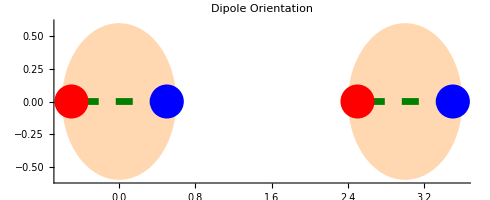

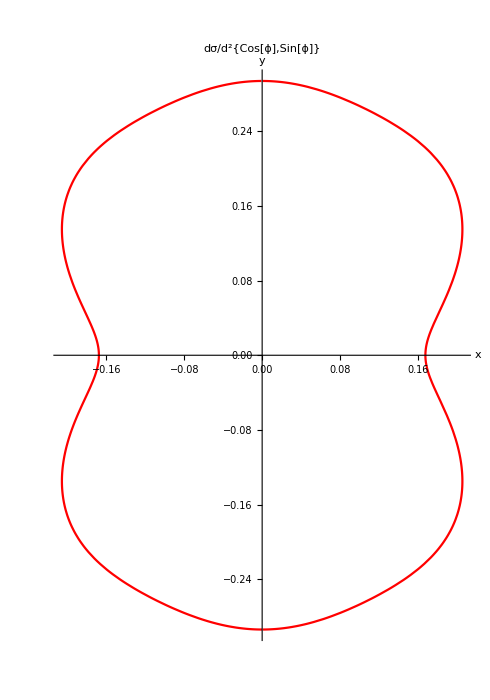

v_2=-0.114285-4.15293×10^-20 ⅈ

```mathematica
x1u={1/2,0};
x2u={-1/2,0};
x3u={1/2,0};
x4u={-1/2,0};
bu={3,0};
kT=1.0;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

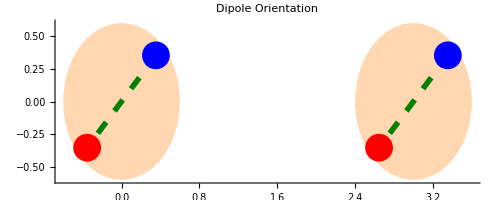

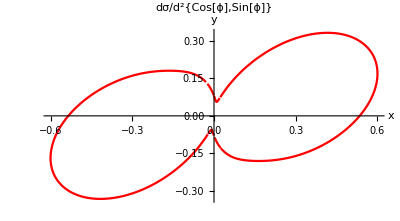

v_2=0.364805+1.18451×10^-18 ⅈ

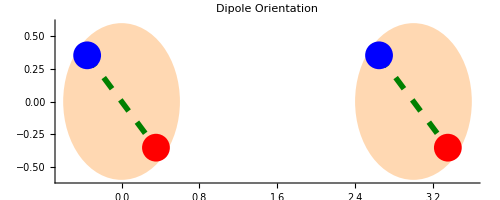

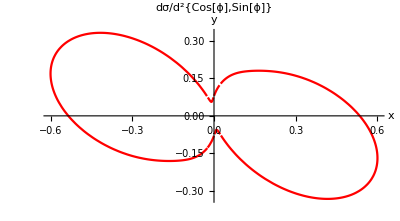

v_2=0.364805+3.09828×10^-18 ⅈ

```mathematica
x1u={1,1}/(2 Sqrt[2]);
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=1.0;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
x1u={-1,1}/(2 Sqrt[2]);
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=1.0;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

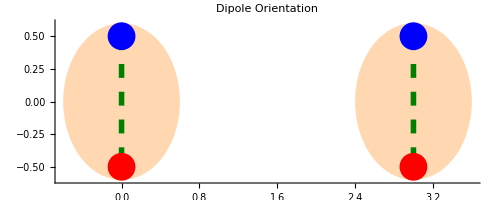

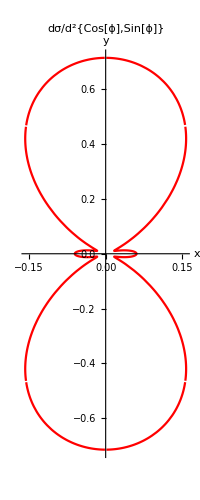

v_2=-0.669888-3.62969×10^-18 ⅈ

```mathematica
x1u={0,1/2};
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=1.0;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

Therefore, we have v2 in hadron - hadron collisions.

### kT>>1/r

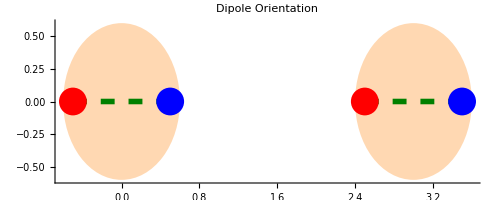

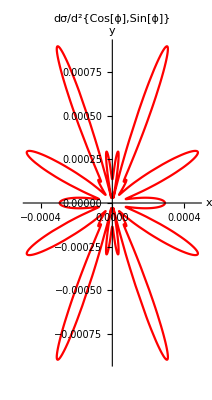

v_2=-0.0641272+0. ⅈ

```mathematica
x1u={1/2,0};
x2u={-1/2,0};
x3u={1/2,0};
x4u={-1/2,0};
bu={3,0};
kT=10.0;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

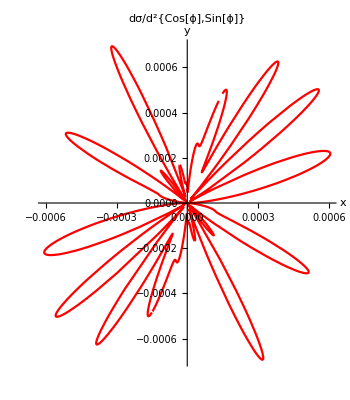

v_2=-0.0142743+0. ⅈ

-Graphics-

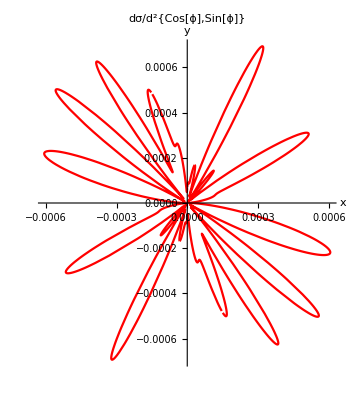

v_2=-0.0142743+0. ⅈ

```mathematica
kT=10.0;
x1u={1,1}/(2 Sqrt[2]);
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
showdσ[bu,x1u,x2u,x3u,x4u,kT]
x1u={-1,1}/(2 Sqrt[2]);
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

-Graphics-

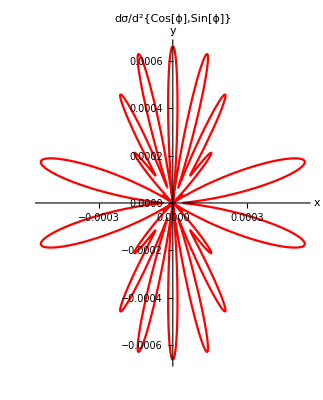

v_2=-0.0402007+0. ⅈ

```mathematica
x1u={0,1/2};
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=10.0;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

Conclusion : for large k_T, the two partons can be treated as independent and the soft gluon can be taken as radiated uncoherently from the two individual partons.

### kT<<1/r

-Graphics-

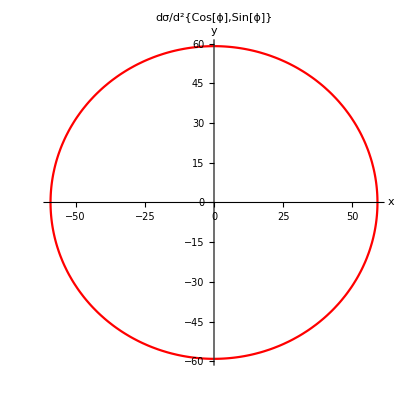

v_2=0.000347844+9.38067×10^-19 ⅈ

```mathematica
x1u={1/2,0};
x2u={-1/2,0};
x3u={1/2,0};
x4u={-1/2,0};
bu={3,0};
kT=0.1;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

-Graphics-

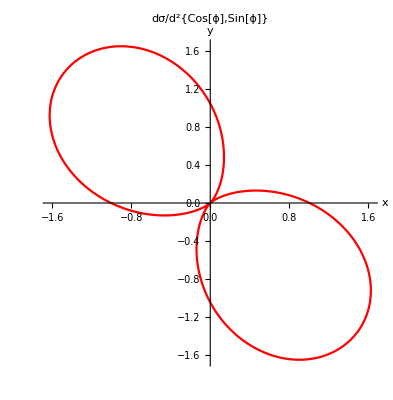

v_2=-0.0103349+8.84144×10^-19 ⅈ

-Graphics-

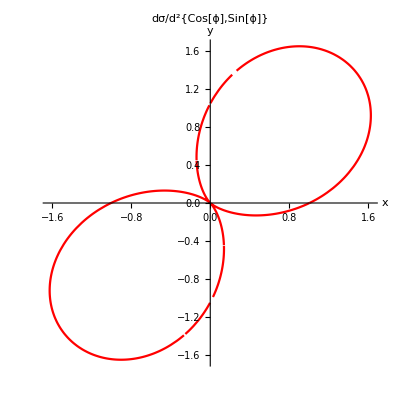

v_2=-0.0103349-2.30944×10^-19 ⅈ

```mathematica
x1u={1,1}/Sqrt[8];
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=0.1;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
x1u={-1,1}/Sqrt[8];
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=0.1;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

-Graphics-

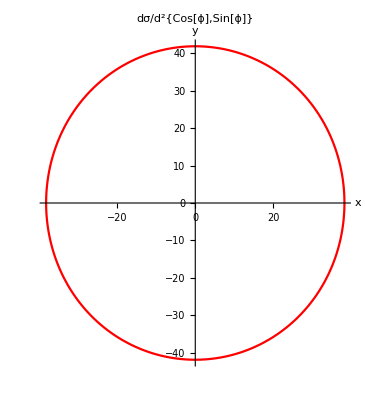

v_2=-0.0226608-1.3638×10^-18 ⅈ

```mathematica
x1u={0,1/2};
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=0.1;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

Conclusion : for small k_T, radiation from the two partons can not distinguish the seperation of the dipole, hence v_2 is also negligible.